## Authors Informations

### Authors : Huan Souza, A. C. Lehum Date : 29/07/2022 Filiation : Universidade Federal do Pará Emails : huan.souza@icen.ufpa.br, lehum@ufpa.br

# Einstein-Yang-Mills with Fermions

```mathematica
Quit[]
```

```mathematica
description="Non-abelian gauge theory with Fermions coupled with linearized gravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","TARCER","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

TARCER 2.0, for more information see the accompanying publication. If you use TARCER in your research, please cite

• R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
$KeepLogDivergentScalelessIntegrals=True;
```

```mathematica
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[rho,TraditionalForm]:="ρ";
MakeBoxes[si,TraditionalForm]:="σ";
MakeBoxes[mt,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(t\)]\)";
MakeBoxes[δ4g,TraditionalForm]:="\!\(\*SubscriptBox[\(δ\), \(4g\)]\)";
MakeBoxes[δ3g,TraditionalForm]:="\!\(\*SubscriptBox[\(δ\), \(3g\)]\)";
MakeBoxes[δ2c,TraditionalForm]:="\!\(\*SubscriptBox[\(δ\), \(2c\)]\)";
MakeBoxes[δ1c,TraditionalForm]:="\!\(\*SubscriptBox[\(δ\), \(1c\)]\)";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
```

```mathematica
ScalarProduct[p,p]=p^2
```

p^2

## 1 - Loop

#### Diagrams

```mathematica
params={InsertionLevel->{Particles},Model->FileNameJoin[{"Einstein_N_Abelian","Einstein_N_Abelian"}],GenericModel->FileNameJoin[{"Einstein_N_Abelian","Einstein_N_Abelian"}],ExcludeParticles->{F[3,{1|2}],F[4,{1|2|3}]}};
top[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible,Tadpoles,WFCorrections,WFCorrectionCTs}];
topTriangle[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,SelfEnergies}];
topGluon[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,Reducible}];
topCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,Reducible}];
topTriangleCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,SelfEnergyCTs}];
{diagQuarkSE,diagQuarkSECT}=(InsertFields[#1,{F[3,{3}]}->{F[3,{3}]},Sequence@@params]&)/@{top[1,1],topCT[1,1]};
{diagGluonSE,diagGluonSECT}=(InsertFields[#1,{V[5]}->{V[5]},Sequence@@params]&)/@{top[1,1],topCT[1,1]};
{diagGhostSE,diagGhostSECT}=(InsertFields[#1,{U[5]}->{U[5]},Sequence@@params]&)/@{top[1,1],topCT[1,1]};
{diagGluonGhostVertex,diagGluonGhostVertexCT}=(InsertFields[#1,{U[5],V[5]}->{U[5]},Sequence@@params]&)/@{topGluon[2,1],topCT[2,1]};
{diagQuarkGluonVertex,diagQuarkGluonVertexCT}=(InsertFields[#1,{F[3,{3}],V[5]}->{F[3,{3}]},Sequence@@params]&)/@{topTriangle[2,1],topTriangleCT[2,1]};
{diagGluonGluonVertex,diagGluonGluonVertexCT}=(InsertFields[#1,{V[5],V[5]}->{V[5]},Sequence@@params]&)/@{topGluon[2,1],topCT[2,1]};
{diagGluonGluonScat,diagGluonGluonScatCT}=(InsertFields[#1,{V[5],V[5]}->{V[5],V[5]},Sequence@@params]&)/@{topGluon[2,2],topCT[2,2]};
```

```mathematica
diag1[0]=diagQuarkSE[[0]][Sequence@@diagQuarkSE,Sequence@@diagQuarkSECT];
diag2[0]=diagGluonSE[[0]][Sequence@@diagGluonSE,Sequence@@diagGluonSECT];
diag3[0]=diagGhostSE[[0]][Sequence@@diagGhostSE,Sequence@@diagGhostSECT];
diag4[0]=diagGluonGhostVertex[[0]][Sequence@@diagGluonGhostVertex,Sequence@@diagGluonGhostVertexCT];
diag5[0]=diagQuarkGluonVertex[[0]][Sequence@@diagQuarkGluonVertex,Sequence@@diagQuarkGluonVertexCT];
diag6[0]=diagGluonGluonVertex[[0]][Sequence@@diagGluonGluonVertex,Sequence@@diagGluonGluonVertexCT];
diag7[0]=diagGluonGluonScat[[0]][Sequence@@diagGluonGluonScat,Sequence@@diagGluonGluonScatCT];
```

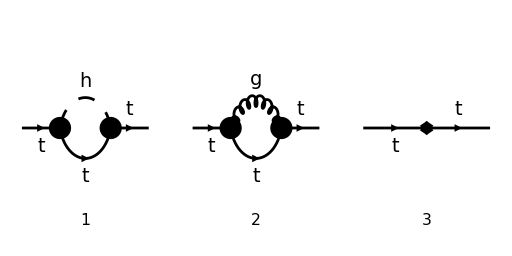

```mathematica
Paint[diag1[0],ColumnsXRows->{3,1},SheetHeader->None,Numbering->Simple,ImageSize->{512,256}];
```

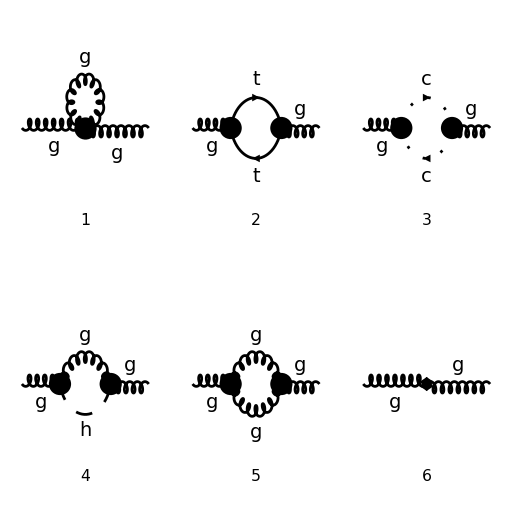

```mathematica
Paint[diag2[0],ColumnsXRows->{3,2},SheetHeader->None,Numbering->Simple,ImageSize->{512,512}];
```

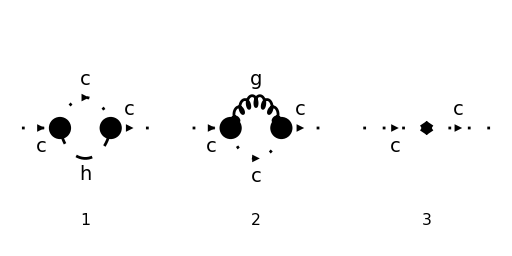

```mathematica
Paint[diag3[0],ColumnsXRows->{3,1},SheetHeader->None,Numbering->Simple,ImageSize->{512,256}];
```

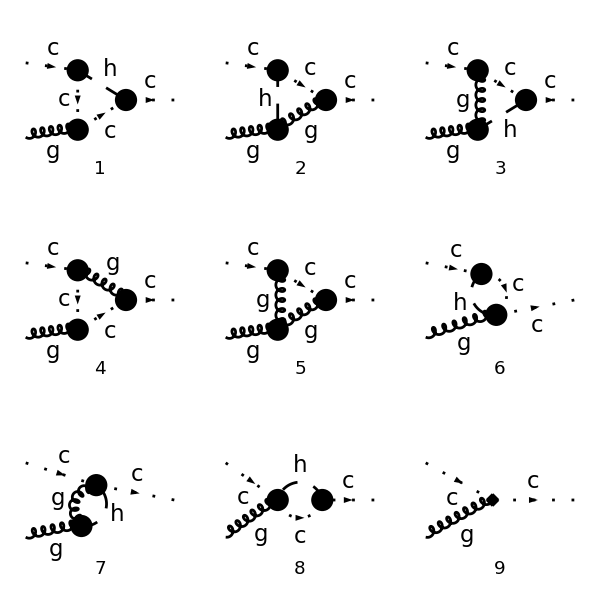

```mathematica
Paint[diag4[0],ColumnsXRows->{3,3},SheetHeader->None,Numbering->Simple,ImageSize->{600,600}];
```

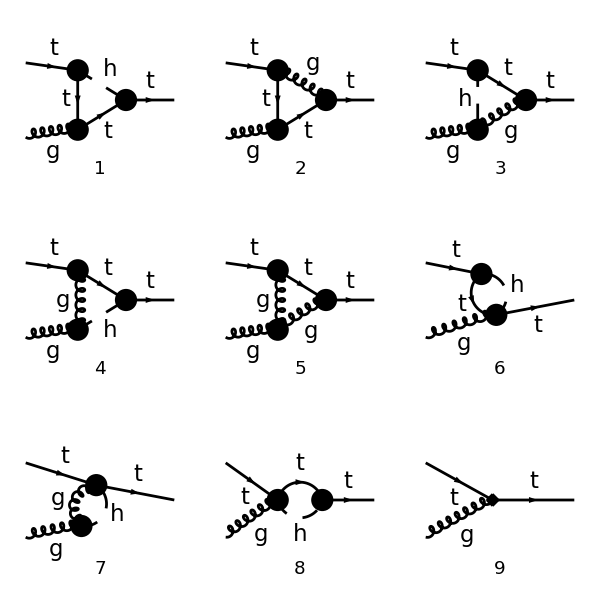

```mathematica
Paint[diag5[0],ColumnsXRows->{3,3},SheetHeader->None,Numbering->Simple,ImageSize->{600,600}];
```

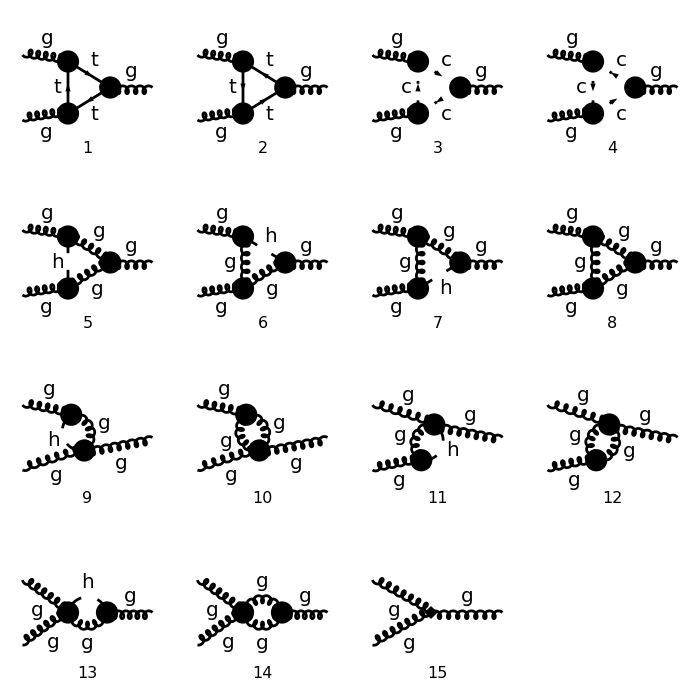

```mathematica
Paint[diag6[0],ColumnsXRows->{4,4},SheetHeader->None,Numbering->Simple,ImageSize->{700,700}];
```

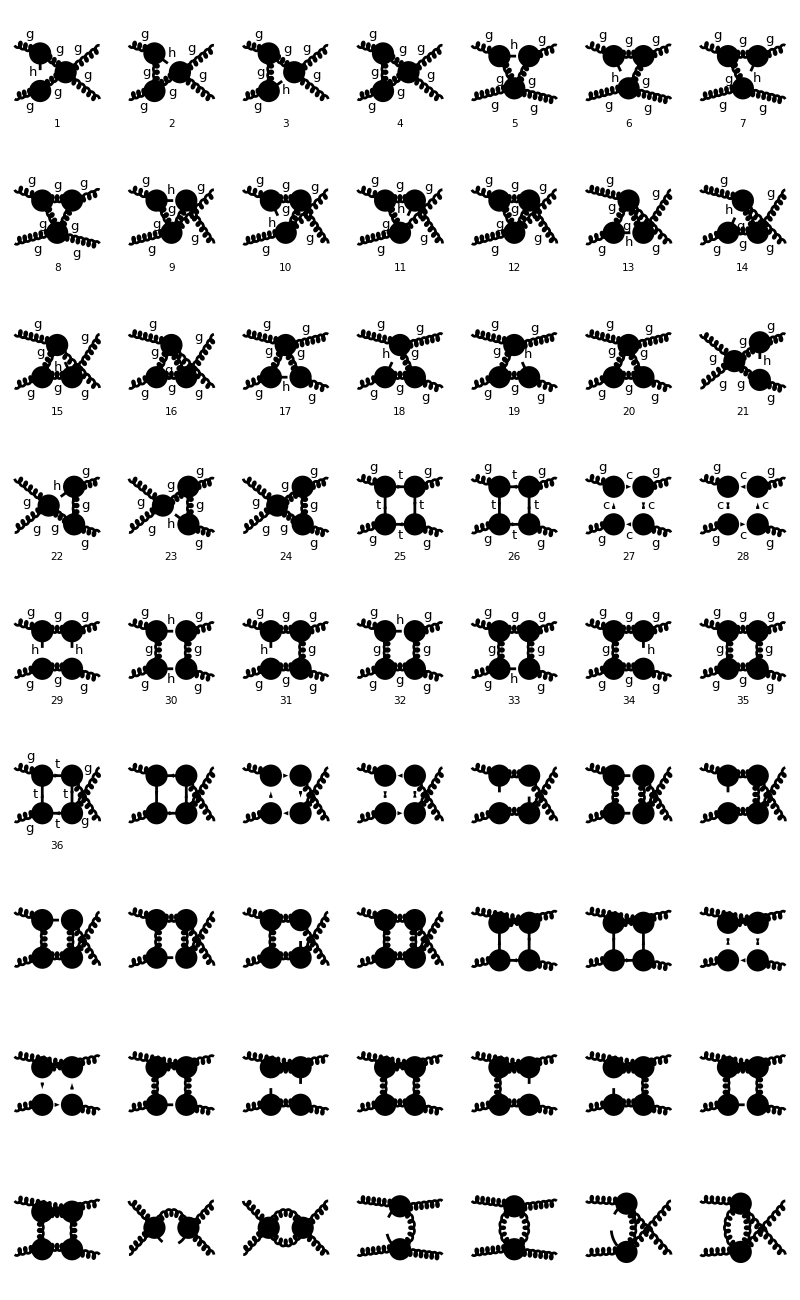

```mathematica
Paint[diag7[0],ColumnsXRows->{7,11},SheetHeader->None,Numbering->Simple,ImageSize->{800,1300}];
```

```mathematica
diag7[1]=DiagramDelete[diag7[0],{29,30,40,41,51,52}];
```

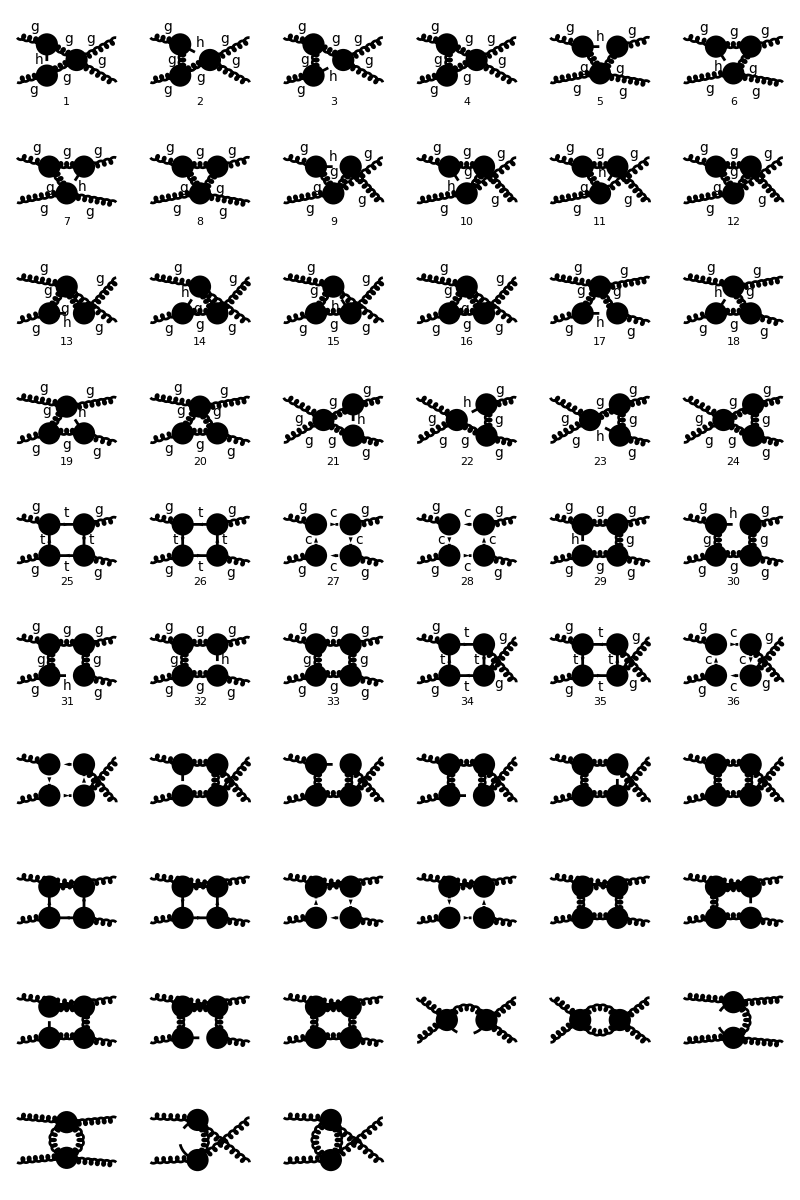

```mathematica
Paint[diag7[1],ColumnsXRows->{6,10},SheetHeader->None,Numbering->Simple,ImageSize->{800,1200}];
```

#### Quark-top self-energy

```mathematica
ampQuarkSE[0]=FCFAConvert[CreateFeynAmp[diag1[0],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p,p},OutgoingMomenta->{p,p},LorentzIndexNames->{mu,nu,α,β},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Contract->True,FinalSubstitutions->{Zm->SMP["Z_m"],Z2->SMP["Z_psi"]}]
```

-(γ^ν.(m_t+γ·l).γ^ν g_s^2 T_Col2Col3^Glu3 T_Col3Col1^Glu3)/((l^2-m_t^2).(l-p)^2)-((γ·(p-l)).(m_t+γ·l).(γ·(l-p)) g_s^2 T_Col2Col3^Glu3 T_Col3Col1^Glu3)/((l^2-m_t^2).((l-p)^2)^2)+((γ·(p-l)).(m_t+γ·l).(γ·(l-p)) ξ_G g_s^2 T_Col2Col3^Glu3 T_Col3Col1^Glu3)/((l^2-m_t^2).((l-p)^2)^2)+1/(2 (l^2-m_t^2).(l-p)^2)(-1/2 ⅈ κ D m_t δ_Col1Col2+1/4 ⅈ κ D γ·l δ_Col1Col2+1/4 ⅈ κ D γ·p δ_Col1Col2-1/4 ⅈ κ γ·(l+p) δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ D m_t+1/4 ⅈ κ D γ·l+1/4 ⅈ κ D γ·p-1/4 ⅈ κ γ·(l+p))-1/(2 (l^2-m_t^2).(l-p)^2)(-1/2 ⅈ κ m_t g^αβ δ_Col1Col2+1/4 ⅈ κ γ·l g^αβ δ_Col1Col2+1/4 ⅈ κ γ·p g^αβ δ_Col1Col2-1/4 ⅈ κ γ^α (l+p)^β δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t g^αβ+1/4 ⅈ κ γ·l g^αβ+1/4 ⅈ κ γ·p g^αβ-1/4 ⅈ κ γ^β (l+p)^α)-1/(2 (l^2-m_t^2).(l-p)^2)(-1/2 ⅈ κ m_t g^αβ δ_Col1Col2+1/4 ⅈ κ γ·l g^αβ δ_Col1Col2+1/4 ⅈ κ γ·p g^αβ δ_Col1Col2-1/4 ⅈ κ γ^α (l+p)^β δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t g^αβ+1/4 ⅈ κ γ·l g^αβ+1/4 ⅈ κ γ·p g^αβ-1/4 ⅈ κ γ^α (l+p)^β)+1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^β δ_Col1Col2-1/4 ⅈ κ γ·(p-l) (l+p)^β δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^β+1/4 ⅈ κ γ·l (p-l)^β+1/4 ⅈ κ γ·p (p-l)^β-1/4 ⅈ κ γ·(p-l) (l+p)^β)+1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^β δ_Col1Col2-1/4 ⅈ κ γ·(p-l) (l+p)^β δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^β+1/4 ⅈ κ γ·l (p-l)^β+1/4 ⅈ κ γ·p (p-l)^β-1/4 ⅈ κ γ^β (p^2-l^2))+1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^α δ_Col1Col2-1/4 ⅈ κ γ^α (p^2-l^2) δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^α+1/4 ⅈ κ γ·l (p-l)^α+1/4 ⅈ κ γ·p (p-l)^α-1/4 ⅈ κ γ·(p-l) (l+p)^α)+1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^α δ_Col1Col2-1/4 ⅈ κ γ^α (p^2-l^2) δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^α+1/4 ⅈ κ γ·l (p-l)^α+1/4 ⅈ κ γ·p (p-l)^α-1/4 ⅈ κ γ^α (p^2-l^2))-1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^β δ_Col1Col2-1/4 ⅈ κ γ·(p-l) (l+p)^β δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^β+1/4 ⅈ κ γ·l (p-l)^β+1/4 ⅈ κ γ·p (p-l)^β-1/4 ⅈ κ γ·(p-l) (l+p)^β) ξ_h-1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^β δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^β δ_Col1Col2-1/4 ⅈ κ γ·(p-l) (l+p)^β δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^β+1/4 ⅈ κ γ·l (p-l)^β+1/4 ⅈ κ γ·p (p-l)^β-1/4 ⅈ κ γ^β (p^2-l^2)) ξ_h-1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^α δ_Col1Col2-1/4 ⅈ κ γ^α (p^2-l^2) δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^α+1/4 ⅈ κ γ·l (p-l)^α+1/4 ⅈ κ γ·p (p-l)^α-1/4 ⅈ κ γ·(p-l) (l+p)^α) ξ_h-1/((l^2-m_t^2).((l-p)^2)^2)(-1/2 ⅈ κ m_t (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·l (p-l)^α δ_Col1Col2+1/4 ⅈ κ γ·p (p-l)^α δ_Col1Col2-1/4 ⅈ κ γ^α (p^2-l^2) δ_Col1Col2).(m_t+γ·l).(-1/2 ⅈ κ m_t (p-l)^α+1/4 ⅈ κ γ·l (p-l)^α+1/4 ⅈ κ γ·p (p-l)^α-1/4 ⅈ κ γ^α (p^2-l^2)) ξ_h-ⅈ m_t (Z_m-1) δ_Col1Col2+ⅈ γ·p (Z_ψ-1) δ_Col1Col2

```mathematica
ampQuarkSE[1]=(TID[#1,l,UsePaVeBasis->True,ToPaVe->True]&)[DiracSimplify[SUNSimplify[ampQuarkSE[0]]]];
```

```mathematica
ampQuarkSEDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampQuarkSE[1]];
```

```mathematica
ampQuarkSEDiv[1]=Simplify[Normal[(Series[#1,{Epsilon,0,0}]&)[FCReplaceD[ampQuarkSEDiv[0],D->4-2*Epsilon]]]]
```

-1/(512 π^2 ε)ⅈ δ_Col1Col2 (m_t (64 ε log(π) C_F ξ_G g_s^2+64 ε log(2) C_F ξ_G g_s^2+32 C_F ξ_G g_s^2-64 ε C_F g_s^2+192 ε log(π) C_F g_s^2+192 ε log(2) C_F g_s^2+96 C_F g_s^2-512 π^2 ε-2 κ^2 ξ_h (p^2 (ε (2+22 log(2)+22 log(π))+11)+m_t^2 (ε (-2+38 log(2)+38 log(π))+19))+κ^2 (γ·p).(γ·p) (-2 ε (-6+53 log(2)+53 log(π))+46 (ε (log(4)+2 log(π))+1) ξ_h-53)+512 π^2 ε Z_m+34 ε κ^2 p^2 log(π)+34 ε κ^2 p^2 log(2)+17 κ^2 p^2-18 ε κ^2 m_t^2+92 ε κ^2 m_t^2 log(π)+92 ε κ^2 m_t^2 log(2)+46 κ^2 m_t^2)+γ·p (-32 C_F g_s^2 (-ε+ε (log(4)+2 log(π)) ξ_G+ξ_G)+512 π^2 ε+κ^2 ξ_h (m_t^2 (ε (-4+58 log(2)+58 log(π))+29)-p^2 (ε (-4+30 log(2)+30 log(π))+15))-10 ε κ^2 p^2+38 ε κ^2 p^2 log(π)+38 ε κ^2 p^2 log(2)+19 κ^2 p^2+18 ε κ^2 m_t^2-74 ε κ^2 m_t^2 log(π)-74 ε κ^2 m_t^2 log(2)-37 κ^2 m_t^2-512 π^2 ε Z_ψ))

```mathematica
ampQuarkSEDiv[2]=(SelectNotFree2[#1,Epsilon,SMP["d_psi"],SMP["d_m"]]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{SMP["Z_psi"]->1+alpha*SMP["d_psi"],SMP["Z_m"]->1+alpha*SMP["d_m"]}&)[ampQuarkSEDiv[1]]]]]]//Simplify
```

-1/(512 π^2 ε)ⅈ δ_Col1Col2 (m_t (32 C_F ξ_G g_s^2+96 C_F g_s^2-2 κ^2 ξ_h (11 p^2+19 m_t^2)+κ^2 (46 ξ_h-53) (γ·p).(γ·p)+512 π^2 ε δ_m+17 κ^2 p^2+46 κ^2 m_t^2)+γ·p (-32 C_F ξ_G g_s^2-512 π^2 ε δ_ψ+κ^2 ξ_h (29 m_t^2-15 p^2)+19 κ^2 p^2-37 κ^2 m_t^2))

```mathematica
ampQuarkSEDiv[3]=(Collect2[#1,DiracGamma,Factoring->Simplify]&)[SUNSimplify[ampQuarkSEDiv[2]]]//Simplify//Expand
```

(ⅈ γ·p ξ_G g_s^2 δ_Col1Col2 C_A^3)/(32 ε π^2)-(ⅈ m_t ξ_G g_s^2 δ_Col1Col2 C_A^3)/(32 ε π^2)-(3 ⅈ m_t g_s^2 δ_Col1Col2 C_A^3)/(32 ε π^2)-(ⅈ C_F γ·p ξ_G g_s^2 δ_Col1Col2 C_A^2)/(16 ε π^2)+(ⅈ C_F m_t ξ_G g_s^2 δ_Col1Col2 C_A^2)/(16 ε π^2)+(3 ⅈ C_F m_t g_s^2 δ_Col1Col2 C_A^2)/(16 ε π^2)+(37 ⅈ κ^2 m_t^2 γ·p δ_Col1Col2 C_A^2)/(512 ε π^2)-(19 ⅈ κ^2 p^2 γ·p δ_Col1Col2 C_A^2)/(512 ε π^2)+(53 ⅈ κ^2 m_t (γ·p).(γ·p) δ_Col1Col2 C_A^2)/(512 ε π^2)-(29 ⅈ κ^2 m_t^2 γ·p ξ_h δ_Col1Col2 C_A^2)/(512 ε π^2)+(15 ⅈ κ^2 p^2 γ·p ξ_h δ_Col1Col2 C_A^2)/(512 ε π^2)-(23 ⅈ κ^2 m_t (γ·p).(γ·p) ξ_h δ_Col1Col2 C_A^2)/(256 ε π^2)+(19 ⅈ κ^2 m_t^3 ξ_h δ_Col1Col2 C_A^2)/(256 ε π^2)+(11 ⅈ κ^2 m_t p^2 ξ_h δ_Col1Col2 C_A^2)/(256 ε π^2)-ⅈ m_t δ_m δ_Col1Col2 C_A^2+ⅈ γ·p δ_ψ δ_Col1Col2 C_A^2-(23 ⅈ κ^2 m_t^3 δ_Col1Col2 C_A^2)/(256 ε π^2)-(17 ⅈ κ^2 m_t p^2 δ_Col1Col2 C_A^2)/(512 ε π^2)-(ⅈ γ·p ξ_G g_s^2 δ_Col1Col2 C_A)/(32 ε π^2)+(ⅈ m_t ξ_G g_s^2 δ_Col1Col2 C_A)/(32 ε π^2)+(3 ⅈ m_t g_s^2 δ_Col1Col2 C_A)/(32 ε π^2)-(37 ⅈ κ^2 C_F m_t^2 γ·p δ_Col1Col2 C_A)/(256 ε π^2)+(19 ⅈ κ^2 C_F p^2 γ·p δ_Col1Col2 C_A)/(256 ε π^2)-(53 ⅈ κ^2 C_F m_t (γ·p).(γ·p) δ_Col1Col2 C_A)/(256 ε π^2)+(29 ⅈ κ^2 C_F m_t^2 γ·p ξ_h δ_Col1Col2 C_A)/(256 ε π^2)-(15 ⅈ κ^2 C_F p^2 γ·p ξ_h δ_Col1Col2 C_A)/(256 ε π^2)+(23 ⅈ κ^2 C_F m_t (γ·p).(γ·p) ξ_h δ_Col1Col2 C_A)/(128 ε π^2)-(19 ⅈ κ^2 C_F m_t^3 ξ_h δ_Col1Col2 C_A)/(128 ε π^2)-(11 ⅈ κ^2 C_F m_t p^2 ξ_h δ_Col1Col2 C_A)/(128 ε π^2)+2 ⅈ C_F m_t δ_m δ_Col1Col2 C_A-2 ⅈ C_F γ·p δ_ψ δ_Col1Col2 C_A+(23 ⅈ κ^2 C_F m_t^3 δ_Col1Col2 C_A)/(128 ε π^2)+(17 ⅈ κ^2 C_F m_t p^2 δ_Col1Col2 C_A)/(256 ε π^2)+(ⅈ C_F γ·p ξ_G g_s^2 δ_Col1Col2)/(16 ε π^2)-(ⅈ C_F m_t ξ_G g_s^2 δ_Col1Col2)/(16 ε π^2)-(3 ⅈ C_F m_t g_s^2 δ_Col1Col2)/(16 ε π^2)

```mathematica
SelectFree2[ampQuarkSEDiv[3],DiracGamma[Momentum[p,D],D].DiracGamma[Momentum[p,D],D]];
ampQuarkSEDiv[4]=Collect2[%,{SMP["d_psi"],SMP["d_m"],DiracGamma[Momentum[p,D],D]},Factoring->Simplify]
```

(ⅈ (C_A-2 C_F) δ_Col1Col2 γ·p (16 (C_A^2-1) ξ_G g_s^2+κ^2 C_A ξ_h (15 p^2-29 m_t^2)+κ^2 C_A (37 m_t^2-19 p^2)))/(512 π^2 ε)-(ⅈ m_t (C_A-2 C_F) δ_Col1Col2 (16 (C_A^2-1) (ξ_G+3) g_s^2-2 κ^2 C_A ξ_h (11 p^2+19 m_t^2)+κ^2 C_A (17 p^2+46 m_t^2)))/(512 π^2 ε)-ⅈ m_t C_A δ_m (C_A-2 C_F) δ_Col1Col2+ⅈ C_A δ_ψ (C_A-2 C_F) δ_Col1Col2 γ·p

```mathematica
a1=Coefficient[ampQuarkSEDiv[4],DiracGamma[Momentum[p,D],D]]//Function[x,Normal[x+O[p]^2]]
a2=SelectFree2[ampQuarkSEDiv[4],DiracGamma]//Function[x,Normal[x+O[p]^2]]
```

ⅈ C_A δ_ψ (C_A-2 C_F) δ_Col1Col2+(ⅈ (C_A-2 C_F) δ_Col1Col2 (16 (C_A^2-1) ξ_G g_s^2-29 κ^2 m_t^2 C_A ξ_h+37 κ^2 m_t^2 C_A))/(512 π^2 ε)

-(ⅈ m_t (C_A-2 C_F) δ_Col1Col2 (16 (C_A^2-1) (ξ_G+3) g_s^2-38 κ^2 m_t^2 C_A ξ_h+46 κ^2 m_t^2 C_A))/(512 π^2 ε)-ⅈ m_t C_A δ_m (C_A-2 C_F) δ_Col1Col2

```mathematica
sol[1]=(#1/.(a_->b_):>a->SUNSimplify[b]&)[Flatten[Solve[a1==0,SMP["d_psi"]]]];
sol[2]=(#1/.(a_->b_):>a->SUNSimplify[b]&)[Flatten[Solve[a2==0/.sol[1],SMP["d_m"]]]];
solMS1=Join[sol[1],sol[2]]//Expand//FullSimplify
```

{δ_ψ→((C_A-2 C_F) (κ^2 m_t^2 C_A (29 ξ_h-37)-16 (C_A^2-1) ξ_G g_s^2))/(512 π^2 ε),δ_m→((C_A-2 C_F) (κ^2 m_t^2 C_A (19 ξ_h-23)-8 (C_A^2-1) (ξ_G+3) g_s^2))/(256 π^2 ε)}

```mathematica
sol[1]=sol[1]/.{CF->(CA^2-1)/(2*CA)}//FullSimplify
δp=SMP["d_psi"]/.sol[1]
```

{δ_ψ→(κ^2 m_t^2 C_A (29 ξ_h-37)-16 (C_A^2-1) ξ_G g_s^2)/(512 π^2 ε C_A)}

(κ^2 m_t^2 C_A (29 ξ_h-37)-16 (C_A^2-1) ξ_G g_s^2)/(512 π^2 ε C_A)

#### Gluon Self-energy

```mathematica
ampGluonSE[0]=SUNSimplify[FCFAConvert[CreateFeynAmp[diag2[0],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu,nu,rho,si},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,Contract->True,FinalSubstitutions->{Z3->SMP["Z_A"]}]]
```

{C_A (-(D g^μν)/l^2+g^μν/l^2+(g^μν l^2)/((l^2)^2)-(ξ_G g^μν l^2)/((l^2)^2)-(l^μ l^ν)/((l^2)^2)+(ξ_G l^μ l^ν)/((l^2)^2)) g_s^2 δ^Glu1Glu2,(tr(-1/2 (m_t-γ·l).γ^ν.(m_t-γ·(l-p)).γ^μ g_s^2 δ^Glu1Glu2))/((l^2-m_t^2).((l-p)^2-m_t^2)),-(C_A (l-p)^μ l^ν g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2),(3 κ^2 p^4 g^μν δ^Glu1Glu2)/(l^2.(l-p)^2)+(κ^2 D^2 p^4 g^μν δ^Glu1Glu2)/(8 l^2.(l-p)^2)-(7 κ^2 D p^4 g^μν δ^Glu1Glu2)/(4 l^2.(l-p)^2)-(3 κ^2 p^4 l^μ l^ν δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 D p^4 l^μ l^ν δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(3 κ^2 p^4 ξ_(T(Gen3)) l^μ l^ν δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 D p^4 ξ_(T(Gen3)) l^μ l^ν δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 p^4 g^μν l^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 p^4 ξ_(T(Gen3)) g^μν l^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 p^2 g^μν l^4 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 p^2 ξ_(T(Gen3)) g^μν l^4 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 p^2 g^μν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 p^2 ξ_(T(Gen3)) g^μν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(4 κ^2 p^2 l^μ l^ν δ^Glu1Glu2)/(l^2.(l-p)^2)+(κ^2 D^2 p^2 l^μ l^ν δ^Glu1Glu2)/(8 l^2.(l-p)^2)-(7 κ^2 D p^2 l^μ l^ν δ^Glu1Glu2)/(4 l^2.(l-p)^2)-(3 κ^2 p^2 p^μ p^ν δ^Glu1Glu2)/(l^2.(l-p)^2)-(κ^2 D^2 p^2 p^μ p^ν δ^Glu1Glu2)/(8 l^2.(l-p)^2)+(7 κ^2 D p^2 p^μ p^ν δ^Glu1Glu2)/(4 l^2.(l-p)^2)-(κ^2 p^2 g^μν l^2 δ^Glu1Glu2)/(l^2.(l-p)^2)-(κ^2 p^2 l^μ l^ν l^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 p^2 ξ_(T(Gen3)) l^μ l^ν l^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 p^2 p^μ p^ν l^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 p^2 ξ_(T(Gen3)) p^μ p^ν l^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(6 κ^2 p^2 g^μν (l·p) δ^Glu1Glu2)/(l^2.(l-p)^2)-(κ^2 D^2 p^2 g^μν (l·p) δ^Glu1Glu2)/(4 l^2.(l-p)^2)+(7 κ^2 D p^2 g^μν (l·p) δ^Glu1Glu2)/(2 l^2.(l-p)^2)+(2 κ^2 p^2 l^μ l^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 p^2 ξ_(T(Gen3)) l^μ l^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(3 κ^2 p^2 p^μ l^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 D p^2 p^μ l^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(3 κ^2 p^2 ξ_(T(Gen3)) p^μ l^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 D p^2 ξ_(T(Gen3)) p^μ l^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(3 κ^2 p^2 l^μ p^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 D p^2 l^μ p^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(3 κ^2 p^2 ξ_(T(Gen3)) l^μ p^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 D p^2 ξ_(T(Gen3)) l^μ p^ν (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(4 κ^2 p^2 g^μν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(4 κ^2 p^2 ξ_(T(Gen3)) g^μν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 g^μν (l·p)^3 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 ξ_(T(Gen3)) g^μν (l·p)^3 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 p^μ p^ν l^4 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 ξ_(T(Gen3)) p^μ p^ν l^4 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(4 κ^2 g^μν (l·p)^2 δ^Glu1Glu2)/(l^2.(l-p)^2)+(κ^2 D^2 g^μν (l·p)^2 δ^Glu1Glu2)/(8 l^2.(l-p)^2)-(7 κ^2 D g^μν (l·p)^2 δ^Glu1Glu2)/(4 l^2.(l-p)^2)-(2 κ^2 p^μ l^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 ξ_(T(Gen3)) p^μ l^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 l^μ p^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 ξ_(T(Gen3)) l^μ p^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(2 κ^2 p^μ p^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 D p^μ p^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(2 κ^2 ξ_(T(Gen3)) p^μ p^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 D ξ_(T(Gen3)) p^μ p^ν (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 g^μν l^2 (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 ξ_(T(Gen3)) g^μν l^2 (l·p)^2 δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 p^μ p^ν l^2 δ^Glu1Glu2)/(l^2.(l-p)^2)-(4 κ^2 p^μ l^ν (l·p) δ^Glu1Glu2)/(l^2.(l-p)^2)-(κ^2 D^2 p^μ l^ν (l·p) δ^Glu1Glu2)/(8 l^2.(l-p)^2)+(7 κ^2 D p^μ l^ν (l·p) δ^Glu1Glu2)/(4 l^2.(l-p)^2)-(4 κ^2 l^μ p^ν (l·p) δ^Glu1Glu2)/(l^2.(l-p)^2)-(κ^2 D^2 l^μ p^ν (l·p) δ^Glu1Glu2)/(8 l^2.(l-p)^2)+(7 κ^2 D l^μ p^ν (l·p) δ^Glu1Glu2)/(4 l^2.(l-p)^2)+(6 κ^2 p^μ p^ν (l·p) δ^Glu1Glu2)/(l^2.(l-p)^2)+(κ^2 D^2 p^μ p^ν (l·p) δ^Glu1Glu2)/(4 l^2.(l-p)^2)-(7 κ^2 D p^μ p^ν (l·p) δ^Glu1Glu2)/(2 l^2.(l-p)^2)+(κ^2 p^μ l^ν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 ξ_(T(Gen3)) p^μ l^ν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(κ^2 l^μ p^ν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(κ^2 ξ_(T(Gen3)) l^μ p^ν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)+(4 κ^2 p^μ p^ν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2)-(4 κ^2 ξ_(T(Gen3)) p^μ p^ν l^2 (l·p) δ^Glu1Glu2)/((l-p)^2.(l^2)^2),-(C_A p^4 g^μν g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)+(C_A p^4 ξ_G g^μν g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)+(C_A p^4 ξ_G^2 l^μ l^ν g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)+(C_A p^4 l^μ l^ν g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)-(C_A p^4 ξ_G l^μ l^ν g_s^2 δ^Glu1Glu2)/((l^2)^2.((l-p)^2)^2)+(5 C_A p^2 g^μν g_s^2 δ^Glu1Glu2)/(2 l^2.(l-p)^2)-(C_A p^2 l^μ l^ν g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A p^2 l^μ l^ν g_s^2 δ^Glu1Glu2)/(l^2.((l-p)^2)^2)+(C_A p^2 ξ_G l^μ l^ν g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A p^2 ξ_G l^μ l^ν g_s^2 δ^Glu1Glu2)/(l^2.((l-p)^2)^2)+(C_A p^2 p^μ p^ν g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)-(C_A p^2 ξ_G p^μ p^ν g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)+(C_A p^2 g^μν l^2 g_s^2 δ^Glu1Glu2)/(l^2.((l-p)^2)^2)-(C_A p^2 ξ_G g^μν l^2 g_s^2 δ^Glu1Glu2)/(l^2.((l-p)^2)^2)-(C_A p^2 ξ_G^2 p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)-(C_A p^2 p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)+(C_A p^2 ξ_G p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/((l^2)^2.((l-p)^2)^2)-(C_A p^2 ξ_G^2 l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)-(C_A p^2 l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)+(C_A p^2 ξ_G l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/((l^2)^2.((l-p)^2)^2)-(C_A g^μν l^4 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A g^μν l^4 g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)+(C_A ξ_G g^μν l^4 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A ξ_G g^μν l^4 g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)-(2 C_A g^μν (l·p)^2 g_s^2 δ^Glu1Glu2)/((l^2)^2.(l-p)^2)+(2 C_A ξ_G g^μν (l·p)^2 g_s^2 δ^Glu1Glu2)/((l^2)^2.(l-p)^2)+(C_A ξ_G^2 p^μ p^ν (l·p)^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)+(C_A p^μ p^ν (l·p)^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.((l-p)^2)^2)-(C_A ξ_G p^μ p^ν (l·p)^2 g_s^2 δ^Glu1Glu2)/((l^2)^2.((l-p)^2)^2)-(3 C_A l^μ l^ν g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)+(2 C_A D l^μ l^ν g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)+(3 C_A p^μ l^ν g_s^2 δ^Glu1Glu2)/(2 l^2.(l-p)^2)-(C_A D p^μ l^ν g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)+(3 C_A l^μ p^ν g_s^2 δ^Glu1Glu2)/(2 l^2.(l-p)^2)-(C_A D l^μ p^ν g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)-(3 C_A p^μ p^ν g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)+(C_A D p^μ p^ν g_s^2 δ^Glu1Glu2)/(2 l^2.(l-p)^2)+(C_A g^μν l^2 g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)+(C_A l^μ l^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A l^μ l^ν l^2 g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)-(C_A ξ_G l^μ l^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A ξ_G l^μ l^ν l^2 g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)-(C_A p^μ l^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A ξ_G p^μ l^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A l^μ p^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A ξ_G l^μ p^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A p^μ p^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A p^μ p^ν l^2 g_s^2 δ^Glu1Glu2)/(l^2.((l-p)^2)^2)+(C_A ξ_G p^μ p^ν l^2 g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A ξ_G p^μ p^ν l^2 g_s^2 δ^Glu1Glu2)/(l^2.((l-p)^2)^2)-(C_A g^μν (l·p) g_s^2 δ^Glu1Glu2)/(l^2.(l-p)^2)-(C_A l^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/((l^2)^2.(l-p)^2)+(C_A ξ_G l^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/((l^2)^2.(l-p)^2)+(3 C_A p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)-(3 C_A ξ_G p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A ξ_G p^μ l^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)+(3 C_A l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)+(C_A l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)-(3 C_A ξ_G l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 (l^2)^2.(l-p)^2)-(C_A ξ_G l^μ p^ν (l·p) g_s^2 δ^Glu1Glu2)/(2 l^2.((l-p)^2)^2)+(2 C_A g^μν l^2 (l·p) g_s^2 δ^Glu1Glu2)/((l^2)^2.(l-p)^2)-(2 C_A ξ_G g^μν l^2 (l·p) g_s^2 δ^Glu1Glu2)/((l^2)^2.(l-p)^2),ⅈ (p^2 g^μν-p^μ p^ν) (1-Z_A) δ^Glu1Glu2}

```mathematica
?DropSumOver
```

```mathematica
ampGluonSE[1]=DiracSimplify[SUNSimplify[ampGluonSE[0][[1]]+Nf*ampGluonSE[0][[2]]+Total[ampGluonSE[0][[3;;All]]]]];
```

```mathematica
ampGluonSE[2]=TID[ampGluonSE[1],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGluonSEDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampGluonSE[2]]//Factor
```

-1/((D-4) (D-1) p^2)ⅈ 2^(-2 D-4) π^(-2 D) δ^Glu1Glu2 (p^2 g^μν-p^μ p^ν) (-2^(D+3) D^2 π^(D+2) κ^2 p^4 ξ_(T(Gen3))-2^(D+4) π^(D+2) κ^2 p^4 ξ_(T(Gen3))+3 2^(D+3) D π^(D+2) κ^2 p^4 ξ_(T(Gen3))+2^(D+4) π^(D+2) p^2 C_A ξ_G g_s^2-2^(D+4) D π^(D+2) p^2 C_A ξ_G g_s^2-3 2^(D+4) π^(D+2) p^2 C_A g_s^2+2^(D+6) D π^(D+2) p^2 C_A g_s^2+2^(2 D+4) D^2 π^(2 D) p^2 Z_A+2^(2 D+6) π^(2 D) p^2 Z_A-5 2^(2 D+4) D π^(2 D) p^2 Z_A+2^D D^3 π^(D+2) κ^2 p^4-2^(D+3) D^2 π^(D+2) κ^2 p^4-2^(2 D+4) D^2 π^(2 D) p^2+2^(D+6) π^(D+2) p^2 N_f g_s^2-2^(D+5) D π^(D+2) p^2 N_f g_s^2-2^(D+8) π^(D+2) m_t^2 N_f g_s^2+2^(D+6) D π^(D+2) m_t^2 N_f g_s^2-3 2^(D+4) π^(D+2) κ^2 p^4+9 D (2 π)^(D+2) κ^2 p^4-2^(2 D+6) π^(2 D) p^2+5 2^(2 D+4) D π^(2 D) p^2)

```mathematica
ampGluonSEDiv[1]=SUNSimplify[Normal[(Series[#1,{Epsilon,0,0}]&)[FCReplaceD[ampGluonSEDiv[0],D->4-2*Epsilon]]]];
```

```mathematica
ampGluonSEDiv[2]=(SelectNotFree2[#1,Epsilon,SMP["d_A"]]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{SMP["Z_A"]->1+alpha*SMP["d_A"],Zxi->1+alpha*SMP["d_A"]}&)[ampGluonSEDiv[1]]]]]]//Factor
```

-(ⅈ δ^Glu1Glu2 (p^2 g^μν-p^μ p^ν) (3 κ^2 p^2 ξ_(T(Gen3))+3 C_A ξ_G g_s^2-13 C_A g_s^2+96 π^2 ε δ_A+4 N_f g_s^2-2 κ^2 p^2))/(96 π^2 ε)

```mathematica
ampGluonSEDiv[3]=Coefficient[ampGluonSEDiv[2],p^2 Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]] Pair[LorentzIndex[nu,D],Momentum[p,D]]]//Expand//Simplify
```

-(ⅈ δ^Glu1Glu2 (3 κ^2 p^2 ξ_(T(Gen3))+3 C_A ξ_G g_s^2-13 C_A g_s^2+96 π^2 ε δ_A+4 N_f g_s^2-2 κ^2 p^2))/(96 π^2 ε)

```mathematica
sol[3]=Simplify[Flatten[Solve[SelectFree2[ampGluonSEDiv[3],p^2]==0,SMP["d_A"]]]]
```

{δ_A→-(g_s^2 (3 C_A ξ_G-13 C_A+4 N_f))/(96 π^2 ε)}

```mathematica
δA=SMP["d_A"]/.%
```

-(g_s^2 (3 C_A ξ_G-13 C_A+4 N_f))/(96 π^2 ε)

#### Ghost self-energy

```mathematica
ampGhostSE[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diag3[0],{1,2,3}],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{μ,ν,α,β},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{Z2c->SMP["Z_u"]}]
```

-g_s^2 l^μ p^ν f^Glu1Glu3Glu4 f^Glu2Glu3Glu4 (((1-ξ_G) (l-p)^μ (p-l)^ν)/(l^2.((l-p)^2)^2)+g^μν/(l^2.(l-p)^2))-(1/2 ⅈ κ g^μν ((l-p)·p)+ⅈ κ p^ν (l-p)^μ) ((g^αν g^βμ+g^αμ g^βν-g^αβ g^μν)/(2 l^2.(l-p)^2)-((1-ξ_h) (l^α l^μ g^βν+l^β l^μ g^αν+l^α l^ν g^βμ+l^β l^ν g^αμ))/((l-p)^2.(l^2)^2)) (-1/2 ⅈ κ g^αβ δ^Glu1Glu2 (p·(p-l))-ⅈ κ p^α δ^Glu1Glu2 (p-l)^β)+ⅈ p^2 (Z_u-1) δ^Glu1Glu2

```mathematica
ampGhostSE[1]=DiracSimplify[SUNSimplify[ampGhostSE[0]]];
```

```mathematica
ampGhostSE[2]=TID[ampGhostSE[1],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGhostSEDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampGhostSE[2]]
```

1/(D-4)ⅈ 2^(-D-4) π^-D p^2 δ^Glu1Glu2 (-8 π^2 C_A ξ_G g_s^2+24 π^2 C_A g_s^2+π^2 D^2 κ^2 p^2+2 π^2 D κ^2 p^2-2^(D+6) π^D Z_u+2^(D+4) D π^D Z_u+2^(D+6) π^D-2^(D+4) D π^D+64 π^2 κ^2 p^2 ξ_h-72 π^2 κ^2 p^2)

```mathematica
ampGhostSEDiv[1]=SUNSimplify[Normal[(Series[#1,{Epsilon,0,0}]&)[FCReplaceD[ampGhostSEDiv[0],D->4-2*Epsilon]]]]
```

1/(128 π^2 ε)ⅈ p^2 δ^Glu1Glu2 (4 ε log(π) C_A ξ_G g_s^2+4 ε log(2) C_A ξ_G g_s^2+2 C_A ξ_G g_s^2-12 ε log(π) C_A g_s^2-12 ε log(2) C_A g_s^2-6 C_A g_s^2-128 π^2 ε-32 ε κ^2 p^2 log(π) ξ_h-32 ε κ^2 p^2 log(2) ξ_h-16 κ^2 p^2 ξ_h+5 ε κ^2 p^2+24 ε κ^2 p^2 log(π)+24 ε κ^2 p^2 log(2)+12 κ^2 p^2+128 π^2 ε Z_u)

```mathematica
ampGhostSEDiv[2]=Simplify[(SelectNotFree2[#1,Epsilon,SMP["d_u"]]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{SMP["Z_u"]->1+alpha*SMP["d_u"]}&)[ampGhostSEDiv[1]]]]]]]//Expand
```

(ⅈ p^2 C_A ξ_G g_s^2 δ^Glu1Glu2)/(64 π^2 ε)-(3 ⅈ p^2 C_A g_s^2 δ^Glu1Glu2)/(64 π^2 ε)-(ⅈ κ^2 p^4 ξ_h δ^Glu1Glu2)/(8 π^2 ε)+(3 ⅈ κ^2 p^4 δ^Glu1Glu2)/(32 π^2 ε)+ⅈ p^2 δ_u δ^Glu1Glu2

```mathematica
ampGhostSEDiv[3]=Coefficient[ampGhostSEDiv[2],p^2]
```

(ⅈ C_A ξ_G g_s^2 δ^Glu1Glu2)/(64 π^2 ε)-(3 ⅈ C_A g_s^2 δ^Glu1Glu2)/(64 π^2 ε)+ⅈ δ_u δ^Glu1Glu2

```mathematica
sol[4]=Simplify[(#1&)[Flatten[Solve[ampGhostSEDiv[3]==0,SMP["d_u"]]]]]
```

{δ_u→-(C_A (ξ_G-3) g_s^2)/(64 π^2 ε)}

```mathematica
δ2c=SMP["d_u"]/.sol[4]
```

-(C_A (ξ_G-3) g_s^2)/(64 π^2 ε)

#### Ghost-Gluon

```mathematica
ampGhostGluon[0]=FCFAConvert[CreateFeynAmp[diag4[0],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3},LorentzIndexNames->{mu,nu},DropSumOver->True,LoopMomenta->{k},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Contract->True]
```

-(2 ⅈ κ^2 p_3^μ (k·p_2)^3 g_s f^Glu1Glu2Glu3)/(k^2.(k+p_2-p_3)^2.((k+26)^2)^2)+1042
 |  |  |  |

```mathematica
ampGhostGluon[1]=DiracSimplify[SUNSimplify[ampGhostGluon[0]]];
```

```mathematica
ampGhostGluon[2]=TID[ampGhostGluon[1],k,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGhostGluonDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampGhostGluon[2]]
```

1/(3 (D-4) (D-1))2^(-D-5) π^-D (-9 κ^2 π^2 p_3^μ (p_1·p_2) g_s f^Glu1Glu2Glu3 D^3+3 κ^2 π^2 p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D^3+15 κ^2 π^2 p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D^3-18 κ^2 π^2 p_3^μ p_2^2 g_s f^Glu1Glu2Glu3 D^3-6 κ^2 π^2 p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D^3+18 κ^2 π^2 p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D^3+3 κ^2 π^2 p_1^μ p_3^2 g_s f^Glu1Glu2Glu3 D^3+6 κ^2 π^2 p_3^μ p_3^2 g_s f^Glu1Glu2Glu3 D^3+24 C_A π^2 ξ_G p_3^μ g_s^3 f^Glu1Glu2Glu3 D^2-24 C_A π^2 p_3^μ g_s^3 f^Glu1Glu2Glu3 D^2+3 2^(D+5) π^D p_3^μ g_s f^Glu1Glu2Glu3 D^2-3 2^(D+5) π^D Z1c p_3^μ g_s f^Glu1Glu2Glu3 D^2+48 κ^2 π^2 ξ_h p_3^μ (p_1·p_2) g_s f^Glu1Glu2Glu3 D^2-96 κ^2 π^2 p_3^μ (p_1·p_2) g_s f^Glu1Glu2Glu3 D^2-16 κ^2 π^2 ξ_h p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D^2+16 κ^2 π^2 p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D^2-32 κ^2 π^2 ξ_h p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D^2+50 κ^2 π^2 p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D^2-48 κ^2 π^2 ξ_h p_3^μ p_2^2 g_s f^Glu1Glu2Glu3 D^2+90 κ^2 π^2 p_3^μ p_2^2 g_s f^Glu1Glu2Glu3 D^2-48 κ^2 π^2 ξ_h p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D^2+84 κ^2 π^2 p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D^2+48 κ^2 π^2 ξ_h p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D^2-90 κ^2 π^2 p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D^2+6 κ^2 π^2 p_3^μ p_3^2 g_s f^Glu1Glu2Glu3 D^2-24 C_A π^2 ξ_G p_3^μ g_s^3 f^Glu1Glu2Glu3 D+120 C_A π^2 p_3^μ g_s^3 f^Glu1Glu2Glu3 D-15 2^(D+5) π^D p_3^μ g_s f^Glu1Glu2Glu3 D+15 2^(D+5) π^D Z1c p_3^μ g_s f^Glu1Glu2Glu3 D+48 κ^2 π^2 ξ_h p_3^μ (p_1·p_2) g_s f^Glu1Glu2Glu3 D+120 κ^2 π^2 p_3^μ (p_1·p_2) g_s f^Glu1Glu2Glu3 D-160 κ^2 π^2 ξ_h p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D+148 κ^2 π^2 p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D-80 κ^2 π^2 ξ_h p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D-112 κ^2 π^2 p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3 D-192 κ^2 π^2 ξ_h p_3^μ p_2^2 g_s f^Glu1Glu2Glu3 D+144 κ^2 π^2 p_3^μ p_2^2 g_s f^Glu1Glu2Glu3 D-48 κ^2 π^2 ξ_h p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D+36 κ^2 π^2 p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D+192 κ^2 π^2 ξ_h p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D-144 κ^2 π^2 p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3 D+48 κ^2 π^2 ξ_h p_1^μ p_3^2 g_s f^Glu1Glu2Glu3 D-132 κ^2 π^2 p_1^μ p_3^2 g_s f^Glu1Glu2Glu3 D+384 κ^2 π^2 ξ_h p_3^μ p_3^2 g_s f^Glu1Glu2Glu3 D-444 κ^2 π^2 p_3^μ p_3^2 g_s f^Glu1Glu2Glu3 D-96 C_A π^2 p_3^μ g_s^3 f^Glu1Glu2Glu3+3 2^(D+7) π^D p_3^μ g_s f^Glu1Glu2Glu3-3 2^(D+7) π^D Z1c p_3^μ g_s f^Glu1Glu2Glu3-96 κ^2 π^2 p_3^μ (p_1·p_2) g_s f^Glu1Glu2Glu3+272 κ^2 π^2 ξ_h p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3-248 κ^2 π^2 p_2^μ (p_1·p_3) g_s f^Glu1Glu2Glu3+64 κ^2 π^2 ξ_h p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3+80 κ^2 π^2 p_3^μ (p_1·p_3) g_s f^Glu1Glu2Glu3+240 κ^2 π^2 ξ_h p_3^μ p_2^2 g_s f^Glu1Glu2Glu3-216 κ^2 π^2 p_3^μ p_2^2 g_s f^Glu1Glu2Glu3-96 κ^2 π^2 ξ_h p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3+48 κ^2 π^2 p_1^μ (p_2·p_3) g_s f^Glu1Glu2Glu3-240 κ^2 π^2 ξ_h p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3+216 κ^2 π^2 p_2^μ (p_2·p_3) g_s f^Glu1Glu2Glu3+96 κ^2 π^2 p_1^μ p_3^2 g_s f^Glu1Glu2Glu3-384 κ^2 π^2 ξ_h p_3^μ p_3^2 g_s f^Glu1Glu2Glu3+432 κ^2 π^2 p_3^μ p_3^2 g_s f^Glu1Glu2Glu3)

```mathematica
ampGhostGluonDiv[1]=SUNSimplify[Normal[(Series[#1,{Epsilon,0,0}]&)[FCReplaceD[ampGhostGluonDiv[0],D->4-2*Epsilon]]]]
```

1/(384 ε π^2)(-12 C_A ξ_G p_3^μ f^Glu1Glu2Glu3 g_s^3+72 κ^2 p_3^μ (p_1·p_2) f^Glu1Glu2Glu3 g_s-40 κ^2 ξ_h p_3^μ (p_1·p_2) f^Glu1Glu2Glu3 g_s-33 κ^2 p_2^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s+26 κ^2 ξ_h p_2^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s-58 κ^2 p_3^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s+32 κ^2 ξ_h p_3^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s-27 κ^2 p_3^μ p_2^2 f^Glu1Glu2Glu3 g_s+54 κ^2 ξ_h p_3^μ p_2^2 f^Glu1Glu2Glu3 g_s-48 κ^2 p_1^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s+44 κ^2 ξ_h p_1^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s+27 κ^2 p_2^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s-54 κ^2 ξ_h p_2^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s+10 κ^2 p_1^μ p_3^2 f^Glu1Glu2Glu3 g_s-8 κ^2 ξ_h p_1^μ p_3^2 f^Glu1Glu2Glu3 g_s+36 κ^2 p_3^μ p_3^2 f^Glu1Glu2Glu3 g_s-48 κ^2 ξ_h p_3^μ p_3^2 f^Glu1Glu2Glu3 g_s)+1/3 (-1/(128 π^4)(-14 C_A π^2 ξ_G p_3^μ f^Glu1Glu2Glu3 g_s^3+6 C_A π^2 p_3^μ f^Glu1Glu2Glu3 g_s^3+384 π^4 Z1c p_3^μ f^Glu1Glu2Glu3 g_s-384 π^4 p_3^μ f^Glu1Glu2Glu3 g_s-36 κ^2 π^2 ξ_h p_3^μ (p_1·p_2) f^Glu1Glu2Glu3 g_s+90 κ^2 π^2 p_3^μ (p_1·p_2) f^Glu1Glu2Glu3 g_s+24 κ^2 π^2 ξ_h p_2^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s-35 κ^2 π^2 p_2^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s+28 κ^2 π^2 ξ_h p_3^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s-84 κ^2 π^2 p_3^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s+48 κ^2 π^2 ξ_h p_3^μ p_2^2 f^Glu1Glu2Glu3 g_s+36 κ^2 π^2 ξ_h p_1^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s-35 κ^2 π^2 p_1^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s-48 κ^2 π^2 ξ_h p_2^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s-4 κ^2 π^2 ξ_h p_1^μ p_3^2 f^Glu1Glu2Glu3 g_s-κ^2 π^2 p_1^μ p_3^2 f^Glu1Glu2Glu3 g_s-32 κ^2 π^2 ξ_h p_3^μ p_3^2 f^Glu1Glu2Glu3 g_s+9 κ^2 π^2 p_3^μ p_3^2 f^Glu1Glu2Glu3 g_s)-((1/4608+(log(2))/1536)/π^4+(log(π))/(1536 π^4)) (288 C_A π^2 ξ_G p_3^μ f^Glu1Glu2Glu3 g_s^3+960 κ^2 π^2 ξ_h p_3^μ (p_1·p_2) f^Glu1Glu2Glu3 g_s-1728 κ^2 π^2 p_3^μ (p_1·p_2) f^Glu1Glu2Glu3 g_s-624 κ^2 π^2 ξ_h p_2^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s+792 κ^2 π^2 p_2^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s-768 κ^2 π^2 ξ_h p_3^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s+1392 κ^2 π^2 p_3^μ (p_1·p_3) f^Glu1Glu2Glu3 g_s-1296 κ^2 π^2 ξ_h p_3^μ p_2^2 f^Glu1Glu2Glu3 g_s+648 κ^2 π^2 p_3^μ p_2^2 f^Glu1Glu2Glu3 g_s-1056 κ^2 π^2 ξ_h p_1^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s+1152 κ^2 π^2 p_1^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s+1296 κ^2 π^2 ξ_h p_2^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s-648 κ^2 π^2 p_2^μ (p_2·p_3) f^Glu1Glu2Glu3 g_s+192 κ^2 π^2 ξ_h p_1^μ p_3^2 f^Glu1Glu2Glu3 g_s-240 κ^2 π^2 p_1^μ p_3^2 f^Glu1Glu2Glu3 g_s+1152 κ^2 π^2 ξ_h p_3^μ p_3^2 f^Glu1Glu2Glu3 g_s-864 κ^2 π^2 p_3^μ p_3^2 f^Glu1Glu2Glu3 g_s))

```mathematica
ampGhostGluonDiv[2]=Simplify[(SelectNotFree2[#1,Epsilon,δ1c]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{Z1c->1+alpha*δ1c}&)[ampGhostGluonDiv[1]]]]]]]
```

-1/(384 π^2 ε)g_s f^Glu1Glu2Glu3 (p_3^μ (12 (C_A ξ_G g_s^2+κ^2 p_3^2 (4 ξ_h-3)+32 π^2 ε δ_(1c))+8 κ^2 (5 ξ_h-9) (p_1·p_2)+2 κ^2 (29-16 ξ_h) (p_1·p_3)+27 κ^2 p_2^2 (1-2 ξ_h))+κ^2 (p_2^μ ((33-26 ξ_h) (p_1·p_3)+27 (2 ξ_h-1) (p_2·p_3))+2 p_1^μ ((24-22 ξ_h) (p_2·p_3)+p_3^2 (4 ξ_h-5))))

```mathematica
ampGhostGluonDiv[3]=SelectFree2[Coefficient[ampGhostGluonDiv[2],Pair[LorentzIndex[mu,D],Momentum[p3,D]]],Momentum]
```

-(C_A ξ_G g_s^3 f^Glu1Glu2Glu3)/(32 π^2 ε)-δ_(1c) g_s f^Glu1Glu2Glu3

```mathematica
sol[4]=Simplify[(#1&)[Flatten[Solve[ampGhostGluonDiv[3]==0,δ1c]]]]
```

{δ_(1c)→-(C_A ξ_G g_s^2)/(32 π^2 ε)}

```mathematica
δ1c=δ1c/.%
```

-(C_A ξ_G g_s^2)/(32 π^2 ε)

#### Gluon-quark vertex

```mathematica
ampQGlVertex[0]=FCFAConvert[CreateFeynAmp[diag5[0],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{0,0},OutgoingMomenta->{0},LorentzIndexNames->{mu,nu,rho},DropSumOver->True,LoopMomenta->{k},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,Contract->True,FinalSubstitutions->{Z3->SMP["Z_A"],Z1->SMP["Z_g"],Z2->SMP["Z_psi"],SMP["m_u"]->SMP["m_q"]}]
```

-(γ^ρ.(m_t+γ·k).γ^μ.(m_t+γ·k).γ^ρ g_s^3 T_Col5Col4^Glu2 T_Col3Col5^Glu4 T_Col4Col1^Glu4)/((k^2-m_t^2)^2.k^2)+((γ·k).(m_t+γ·k).γ^μ.(m_t+γ·k).(γ·k) g_s^3 T_Col5Col4^Glu2 T_Col3Col5^Glu4 T_Col4Col1^Glu4)/((k^2-m_t^2)^2.(k^2)^2)-((γ·k).(m_t+γ·k).γ^μ.(m_t+γ·k).(γ·k) ξ_G g_s^3 T_Col5Col4^Glu2 T_Col3Col5^Glu4 T_Col4Col1^Glu4)/((k^2-m_t^2)^2.(k^2)^2)+(ⅈ γ^μ.(m_t-γ·k).(γ·k) g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^2.(k^2-m_t^2))+(ⅈ (γ·k).(m_t-γ·k).γ^μ g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^2.(k^2-m_t^2))-(2 ⅈ γ^ν.(m_t-γ·k).γ^ν k^μ g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^2.(k^2-m_t^2))+(2 ⅈ (γ·k).(m_t-γ·k).(γ·k) k^μ g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^3.(k^2-m_t^2))-(2 ⅈ (γ·k).(m_t-γ·k).(γ·k) ξ_G k^μ g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^3.(k^2-m_t^2))-(ⅈ γ^μ.(m_t-γ·k).(γ·k) k^2 g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^3.(k^2-m_t^2))-(ⅈ (γ·k).(m_t-γ·k).γ^μ k^2 g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^3.(k^2-m_t^2))+(ⅈ γ^μ.(m_t-γ·k).(γ·k) ξ_G k^2 g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^3.(k^2-m_t^2))+(ⅈ (γ·k).(m_t-γ·k).γ^μ ξ_G k^2 g_s^3 f^Glu2Glu4Glu5 T_Col4Col1^Glu4 T_Col3Col4^Glu5)/((k^2)^3.(k^2-m_t^2))+((-1/2 ⅈ κ D m_t-1/4 ⅈ κ γ·k+1/4 ⅈ κ D γ·k).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ D m_t-1/4 ⅈ κ γ·k+1/4 ⅈ κ D γ·k) g_s T_Col3Col1^Glu2)/(2 (k^2-m_t^2)^2.k^2)-((-1/2 ⅈ κ m_t g^νρ+1/4 ⅈ κ γ·k g^νρ-1/4 ⅈ κ γ^ρ k^ν).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t g^νρ+1/4 ⅈ κ γ·k g^νρ-1/4 ⅈ κ γ^ν k^ρ) g_s T_Col3Col1^Glu2)/(2 (k^2-m_t^2)^2.k^2)-((-1/2 ⅈ κ m_t g^νρ+1/4 ⅈ κ γ·k g^νρ-1/4 ⅈ κ γ^ν k^ρ).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t g^νρ+1/4 ⅈ κ γ·k g^νρ-1/4 ⅈ κ γ^ν k^ρ) g_s T_Col3Col1^Glu2)/(2 (k^2-m_t^2)^2.k^2)+((-1/2 ⅈ κ m_t k^ν).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)+((-1/2 ⅈ κ m_t k^ρ).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)+((-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)+((-1/2 ⅈ κ m_t k^ρ+1/4 ⅈ κ γ·k k^ρ-1/4 ⅈ κ γ^ρ k^2).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)-((-1/2 ⅈ κ m_t k^ν).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2) ξ_(T(Gen5)) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)-((-1/2 ⅈ κ m_t k^ρ).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ) ξ_(T(Gen5)) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)-((-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2) ξ_(T(Gen5)) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)-((-1/2 ⅈ κ m_t k^ρ+1/4 ⅈ κ γ·k k^ρ-1/4 ⅈ κ γ^ρ k^2).(m_t+γ·k).γ^μ.(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ) ξ_(T(Gen5)) g_s T_Col3Col1^Glu2)/((k^2-m_t^2)^2.(k^2)^2)-ⅈ γ^μ (Z_g-1) T_Col3Col1^Glu2 g_s+((-1/2 ⅈ κ D m_t+1/4 ⅈ κ γ·k-1/4 ⅈ κ D γ·k).(m_t-γ·k).(1/2 ⅈ κ γ^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ D γ^μ g_s T_Col3Col1^Glu2))/(2 (k^2-m_t^2).k^2)-((-1/2 ⅈ κ m_t g^νρ-1/4 ⅈ κ γ·k g^νρ+1/4 ⅈ κ γ^ν k^ρ).(m_t-γ·k).(1/2 ⅈ κ γ^ρ g^μν g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ g^νρ g_s T_Col3Col1^Glu2))/(2 (k^2-m_t^2).k^2)-((-1/2 ⅈ κ m_t g^νρ-1/4 ⅈ κ γ·k g^νρ+1/4 ⅈ κ γ^ν k^ρ).(m_t-γ·k).(1/2 ⅈ κ γ^ν g^μρ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ g^νρ g_s T_Col3Col1^Glu2))/(2 (k^2-m_t^2).k^2)+((1/2 ⅈ κ γ^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ D γ^μ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ D m_t-1/4 ⅈ κ γ·k+1/4 ⅈ κ D γ·k))/(2 (k^2-m_t^2).k^2)-((1/2 ⅈ κ γ^ρ g^μν g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ g^νρ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t g^νρ+1/4 ⅈ κ γ·k g^νρ-1/4 ⅈ κ γ^ν k^ρ))/(2 (k^2-m_t^2).k^2)-((1/2 ⅈ κ γ^ν g^μρ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ g^νρ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t g^νρ+1/4 ⅈ κ γ·k g^νρ-1/4 ⅈ κ γ^ν k^ρ))/(2 (k^2-m_t^2).k^2)+((-1/2 ⅈ κ m_t k^ρ).(m_t-γ·k).(1/2 ⅈ κ γ·k g^μρ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2))/((k^2-m_t^2).(k^2)^2)+((-1/2 ⅈ κ m_t k^ρ).(m_t-γ·k).(1/2 ⅈ κ γ^ρ k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2))/((k^2-m_t^2).(k^2)^2)+((-1/2 ⅈ κ m_t k^ν-1/4 ⅈ κ γ·k k^ν+1/4 ⅈ κ γ^ν k^2).(m_t-γ·k).(1/2 ⅈ κ γ·k g^μν g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2))/((k^2-m_t^2).(k^2)^2)+((-1/2 ⅈ κ m_t k^ν-1/4 ⅈ κ γ·k k^ν+1/4 ⅈ κ γ^ν k^2).(m_t-γ·k).(1/2 ⅈ κ γ^ν k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2))/((k^2-m_t^2).(k^2)^2)+((1/2 ⅈ κ γ·k g^μν g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2))/((k^2-m_t^2).(k^2)^2)+((1/2 ⅈ κ γ^ν k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2))/((k^2-m_t^2).(k^2)^2)+((1/2 ⅈ κ γ·k g^μρ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ))/((k^2-m_t^2).(k^2)^2)+((1/2 ⅈ κ γ^ρ k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ))/((k^2-m_t^2).(k^2)^2)-((-1/2 ⅈ κ m_t k^ρ).(m_t-γ·k).(1/2 ⅈ κ γ·k g^μρ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((-1/2 ⅈ κ m_t k^ρ).(m_t-γ·k).(1/2 ⅈ κ γ^ρ k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((-1/2 ⅈ κ m_t k^ν-1/4 ⅈ κ γ·k k^ν+1/4 ⅈ κ γ^ν k^2).(m_t-γ·k).(1/2 ⅈ κ γ·k g^μν g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((-1/2 ⅈ κ m_t k^ν-1/4 ⅈ κ γ·k k^ν+1/4 ⅈ κ γ^ν k^2).(m_t-γ·k).(1/2 ⅈ κ γ^ν k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((1/2 ⅈ κ γ·k g^μν g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((1/2 ⅈ κ γ^ν k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ν g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ν+1/4 ⅈ κ γ·k k^ν-1/4 ⅈ κ γ^ν k^2) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((1/2 ⅈ κ γ·k g^μρ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)-((1/2 ⅈ κ γ^ρ k^μ g_s T_Col3Col1^Glu2-1/2 ⅈ κ γ^μ k^ρ g_s T_Col3Col1^Glu2).(m_t+γ·k).(-1/2 ⅈ κ m_t k^ρ) ξ_(T(Gen5)))/((k^2-m_t^2).(k^2)^2)

```mathematica
ampQGlVertex[1]=DiracSimplify[SUNSimplify[ampQGlVertex[0]]];
```

```mathematica
ampQGlVertex[2]=TID[ampQGlVertex[1],k,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampQGlVertexDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampQGlVertex[2]]
```

1/((D-4) (D-1) D)2^(-D-4) π^-D (ⅈ κ^2 m_t^2 π^2 γ^μ g_s T_Col3Col1^Glu2 D^4+ⅈ 2^(D+4) π^D γ^μ g_s T_Col3Col1^Glu2 D^3-3 ⅈ κ^2 m_t^2 π^2 γ^μ g_s T_Col3Col1^Glu2 D^3-2 ⅈ κ^2 m_t^2 π^2 γ^μ ξ_(T(Gen5)) g_s T_Col3Col1^Glu2 D^3-ⅈ 2^(D+4) π^D γ^μ g_s Z_g T_Col3Col1^Glu2 D^3+32 ⅈ π^2 γ^μ g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1 D^3-5 ⅈ 2^(D+4) π^D γ^μ g_s T_Col3Col1^Glu2 D^2+30 ⅈ κ^2 m_t^2 π^2 γ^μ g_s T_Col3Col1^Glu2 D^2-18 ⅈ κ^2 m_t^2 π^2 γ^μ ξ_(T(Gen5)) g_s T_Col3Col1^Glu2 D^2+5 ⅈ 2^(D+4) π^D γ^μ g_s Z_g T_Col3Col1^Glu2 D^2+64 π^2 γ^μ g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1 D^2+64 π^2 γ^μ ξ_G g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1 D^2-160 ⅈ π^2 γ^μ g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1 D^2+32 ⅈ π^2 γ^μ ξ_G g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1 D^2+ⅈ 2^(D+6) π^D γ^μ g_s T_Col3Col1^Glu2 D-52 ⅈ κ^2 m_t^2 π^2 γ^μ g_s T_Col3Col1^Glu2 D+48 ⅈ κ^2 m_t^2 π^2 γ^μ ξ_(T(Gen5)) g_s T_Col3Col1^Glu2 D-ⅈ 2^(D+6) π^D γ^μ g_s Z_g T_Col3Col1^Glu2 D-128 π^2 γ^μ g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1 D-128 π^2 γ^μ ξ_G g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1 D+128 ⅈ π^2 γ^μ g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1 D-64 ⅈ π^2 γ^μ ξ_G g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1 D+108 ⅈ κ^2 m_t^2 π^2 γ^μ g_s T_Col3Col1^Glu2-124 ⅈ κ^2 m_t^2 π^2 γ^μ ξ_(T(Gen5)) g_s T_Col3Col1^Glu2+64 π^2 γ^μ g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1+64 π^2 γ^μ ξ_G g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1+128 ⅈ π^2 γ^μ ξ_G g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1)

```mathematica
ampQGlVertexDiv[1]=SUNSimplify[Normal[(Series[#1,{Epsilon,0,0}]&)[FCReplaceD[ampQGlVertexDiv[0],D->4-2*Epsilon]]]];
```

```mathematica
ampQGlVertexDiv[2]=Simplify[(SelectNotFree2[#1,Epsilon,SMP["d_g"]]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{SMP["Z_g"]->1+alpha*SMP["d_g"]}&)[ampQGlVertexDiv[1]]]]]]]
```

-1/(512 π^2 ε)ⅈ γ^μ g_s (T_Col3Col1^Glu2 (-29 κ^2 m_t^2 ξ_(T(Gen5))+512 π^2 ε δ_g+37 κ^2 m_t^2)-16 ⅈ g_s^2 (3 (ξ_G+1) f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1+2 ⅈ ξ_G (T^Glu4 T^Glu2 T^Glu4)_Col3Col1))

```mathematica
ampQGlVertexDiv[3]=(Collect2[#1,Epsilon,SUNIndex]&)[(#1/.SUNTrace[x__]:>SUNTrace[x,Explicit->True]&)[(SUNSimplify[#1,Explicit->True]&)[ampQGlVertexDiv[2]]]]
```

(ⅈ κ^2 m_t^2 γ^μ g_s T_Col3Col1^Glu2 (29 ξ_(T(Gen5))-37))/(512 π^2 ε)-(3 γ^μ (ξ_G+1) g_s^3 f^(Glu2Glu5FCGV(c22804)(0)) (T^Glu5 T^(FCGV(c22804)(0)))_Col3Col1)/(32 π^2 ε)-(ⅈ γ^μ ξ_G g_s^3 (T^Glu4 T^Glu2 T^Glu4)_Col3Col1)/(16 π^2 ε)-ⅈ γ^μ δ_g g_s T_Col3Col1^Glu2

```mathematica
ampQGlVertexDiv[4]=(Collect2[#1,SMP]&)[SUNSimplify[(#1/.suntf[xx_,_SUNFIndex,_SUNFIndex]:>SUNT@@xx&)[(#1/.SUNTF->suntf&)[(#1/.suntf[xx_,_SUNFIndex,_SUNFIndex]:>SUNT@@xx&)[ampQGlVertexDiv[3]]]]]]
```

(ⅈ κ^2 m_t^2 C_A γ^μ g_s T^Glu2 (C_A-2 C_F) (29 ξ_(T(Gen5))-37))/(512 π^2 ε)-(ⅈ γ^μ g_s^3 T^Glu2 (C_A-2 C_F) (3 C_A^2 ξ_G+3 C_A^2-2 ξ_G))/(64 π^2 ε)-ⅈ C_A γ^μ δ_g g_s T^Glu2 (C_A-2 C_F)

```mathematica
ampQGlVertexDiv[5]=SUNSimplify[(Collect2[#1,Epsilon]&)[ampQGlVertexDiv[4]/.{SMP["d_A"]->SMP["d_A^MS"],SMP["d_psi"]->SMP["d_psi^MS"],SMP["d_g"]->SMP["d_g"],SMP["Delta"]->1/Epsilon}]]
```

-(ⅈ γ^μ g_s T^Glu2 (C_A-2 C_F) (-29 κ^2 m_t^2 C_A ξ_(T(Gen5))+24 C_A^2 ξ_G g_s^2+512 π^2 ε C_A δ_g+24 C_A^2 g_s^2+37 κ^2 m_t^2 C_A-16 ξ_G g_s^2))/(512 π^2 ε)

```mathematica
sol[5]=Simplify[Flatten[Solve[SelectFree2[ampQGlVertexDiv[5],p1,p2,p3]==0,SMP["d_g"]]]]//Simplify//StandardForm
```

{SMP[d_g]→(-37 κ^2 CA mt^2+29 κ^2 CA mt^2 GaugeXi[T[Gen5]]-8 (3 CA^2+(-2+3 CA^2) GaugeXi[G]) SMP[g_s]^2)/(512 CA Epsilon π^2)}

```mathematica
SUNSimplify[(-37 ("κ")^2 CA mt^2+29 ("κ")^2 CA mt^2 GaugeXi["h"]-8 (3 CA^2+(-2+3 CA^2) GaugeXi["G"]) SMP["g_s"]^2)/(512 CA Epsilon π^2)]//FullSimplify
```

((C_A-2 C_F) (κ^2 m_t^2 C_A (29 ξ_h-37)-8 g_s^2 ((3 C_A^2-2) ξ_G+3 C_A^2)))/(512 π^2 ε)

```mathematica
%/.{CF->(CA^2-1)/(2*CA)}
```

((C_A-(C_A^2-1)/C_A) (κ^2 m_t^2 C_A (29 ξ_h-37)-8 g_s^2 ((3 C_A^2-2) ξ_G+3 C_A^2)))/(512 π^2 ε)

```mathematica
%//Expand
```

-(3 C_A ξ_G g_s^2)/(64 π^2 ε)+(ξ_G g_s^2)/(32 π^2 ε C_A)-(3 C_A g_s^2)/(64 π^2 ε)+(29 κ^2 m_t^2 ξ_h)/(512 π^2 ε)-(37 κ^2 m_t^2)/(512 π^2 ε)

```mathematica
δg=%
```

-(3 C_A ξ_G g_s^2)/(64 π^2 ε)+(ξ_G g_s^2)/(32 π^2 ε C_A)-(3 C_A g_s^2)/(64 π^2 ε)+(29 κ^2 m_t^2 ξ_h)/(512 π^2 ε)-(37 κ^2 m_t^2)/(512 π^2 ε)

#### Gluon-Gluon Vertex

```mathematica
ampGlGlVertex[0]=FCTraceFactor[FCFAConvert[CreateFeynAmp[diag6[0],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3},LorentzIndexNames->{mu,nu,α},DropSumOver->True,LoopMomenta->{k},UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,Contract->True]]
```

{(tr((m_t+γ·(k+p_2-p_3)).γ^α.(26+1).1.(m_t+γ·k).γ^μ) 3 1)/((k^2-m_t^2).((k+1)^2-26^2).((k+26-p_3)^2-m_t^2)),13,7+1}
 |  |  |  |

```mathematica
ampGlGlVertex[1]=DiracSimplify[Nf*Total[ampGlGlVertex[0][[1;;2]]]+Total[ampGlGlVertex[0][[3;;All]]]]
```

-(2 ⅈ κ^2 p_3^μ g^να (k·p_2)^3 g_s f^Glu1Glu2Glu3)/(k^2.(k+p_2-p_3)^2.((k+26)^2)^2)+12855
 |  |  |  |

```mathematica
ampGlGlVertex[2]=TID[Contract[1/4*MTD[mu,nu]*ampGlGlVertex[1]]/.{-p3->-p1-p2,p3->p1+p2},k,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGlGlVertexDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampGlGlVertex[2]];
```

```mathematica
ampGlGlVertexDiv[1]=SUNSimplify[ampGlGlVertexDiv[0],Explicit->True];
```

```mathematica
ampGlGlVertexDiv[2]=ampGlGlVertexDiv[1]/.{SUNTrace[x__]:>SUNTrace[x,Explicit->True]};
```

```mathematica
ampGlGlVertexDiv[3]=(SelectNotFree2[#1,Epsilon,Z3g]&)[(Normal[Series[#1,{Epsilon,0,0}]]&)[FCReplaceD[ampGlGlVertexDiv[2],D->4-2*Epsilon]]]
```

-(5 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)-(ⅈ N_f p_1^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)+(5 ⅈ C_A p_1^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(5 ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(ⅈ N_f p_2^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)-(5 ⅈ C_A p_2^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(5 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(ⅈ N_f p_1^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)-(5 ⅈ C_A p_1^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)-(5 ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)-(ⅈ N_f p_2^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)+(5 ⅈ C_A p_2^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(7 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)+(ⅈ N_f p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)+(3 ⅈ C_A p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)+(ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)+(ⅈ N_f p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)+(13 ⅈ C_A p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(7 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)-(ⅈ N_f p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)-(3 ⅈ C_A p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)-(ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(ⅈ N_f p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(13 ⅈ C_A p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(C_A ξ_G p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(N_f p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(13 C_A p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(7 C_A ξ_G p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)-(N_f p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)-(3 C_A p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)-(C_A ξ_G p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(N_f p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(13 C_A p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(7 C_A ξ_G p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)-(N_f p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)-(3 C_A p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)-(17 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(29 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(19 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)-(95 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(25 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(59 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(59 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(19 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)+(95 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)+(17 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(29 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(17 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(29 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(19 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)+(95 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)+(25 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(59 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(59 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(19 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)-(95 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(17 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(29 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(2 ⅈ Z3g (π^4+2 π^4 log(2)+2 π^4 log(π)) p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/π^4+(ⅈ Z3g (π^4 log(2)+π^4 log(π)) p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(6 π^4)+(2 ⅈ Z3g (3 π^4+4 π^4 log(2)+4 π^4 log(π)) p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(3 π^4)+(3 ⅈ Z3g (π^4+4 π^4 log(2)+4 π^4 log(π)) p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(8 π^4)+(47 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)+(95 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(5 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(18 ε π^2)+(901 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)+(35 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(128 ε π^2)+(7 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε π^2)+(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(96 ε π^2)+(497 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(768 ε π^2)+(161 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(415 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(13 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)+(391 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(25 ⅈ Z3g p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε)-(25 ⅈ p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε)-(2 ⅈ Z3g (π^4+2 π^4 log(2)+2 π^4 log(π)) p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/π^4-(ⅈ Z3g (π^4 log(2)+π^4 log(π)) p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(6 π^4)-12800 ⅈ π^4 Z3g ((1/9216+(log(2))/3072)/π^4+(log(π))/(3072 π^4)) p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s-(25 ⅈ Z3g p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε)-(25 ⅈ p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε)-(2 ⅈ Z3g (3 π^4+4 π^4 log(2)+4 π^4 log(π)) p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(3 π^4)-(3 ⅈ Z3g (π^4+4 π^4 log(2)+4 π^4 log(π)) p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(8 π^4)-12800 ⅈ π^4 Z3g ((1/9216+(log(2))/3072)/π^4+(log(π))/(3072 π^4)) p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s-(47 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(95 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(5 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(18 ε π^2)-(901 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(35 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(128 ε π^2)-(7 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε π^2)-(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(96 ε π^2)-(497 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(768 ε π^2)-(161 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(415 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(13 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(391 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(25 Z3g p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε)-(25 p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε)-(2 Z3g (3 π^4+4 π^4 log(2)+4 π^4 log(π)) p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(3 π^4)-(3 Z3g (π^4+4 π^4 log(2)+4 π^4 log(π)) p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(8 π^4)-12800 π^4 Z3g ((1/9216+(log(2))/3072)/π^4+(log(π))/(3072 π^4)) p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s-(25 Z3g p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε)-(25 p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε)-(2 Z3g (π^4+2 π^4 log(2)+2 π^4 log(π)) p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/π^4-(Z3g (π^4 log(2)+π^4 log(π)) p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(6 π^4)-12800 π^4 Z3g ((1/9216+(log(2))/3072)/π^4+(log(π))/(3072 π^4)) p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s-(13 κ^2 ξ_h p_1^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(391 κ^2 p_1^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(161 κ^2 ξ_h p_2^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(415 κ^2 p_2^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(25 κ^2 ξ_h p_1^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(96 ε π^2)-(497 κ^2 p_1^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(768 ε π^2)-(35 κ^2 ξ_h p_2^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(128 ε π^2)-(7 κ^2 p_2^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε π^2)-(5 κ^2 ξ_h p_1^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(18 ε π^2)-(901 κ^2 p_1^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(47 κ^2 ξ_h p_2^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(95 κ^2 p_2^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(2 Z3g (3 π^4+4 π^4 log(2)+4 π^4 log(π)) p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(3 π^4)-(3 Z3g (π^4+4 π^4 log(2)+4 π^4 log(π)) p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(8 π^4)-(2 Z3g (π^4+2 π^4 log(2)+2 π^4 log(π)) p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/π^4-(Z3g (π^4 log(2)+π^4 log(π)) p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(6 π^4)-(13 κ^2 ξ_h p_1^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(391 κ^2 p_1^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(161 κ^2 ξ_h p_2^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(415 κ^2 p_2^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(25 κ^2 ξ_h p_1^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(96 ε π^2)-(497 κ^2 p_1^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(768 ε π^2)-(35 κ^2 ξ_h p_2^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(128 ε π^2)-(7 κ^2 p_2^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(12 ε π^2)-(5 κ^2 ξ_h p_1^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(18 ε π^2)-(901 κ^2 p_1^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(47 κ^2 ξ_h p_2^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(95 κ^2 p_2^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(576 ε π^2)

```mathematica
ampGlGlVertexDiv[4]=(SelectNotFree2[#1,Epsilon,δ3g]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{Z3g->1+alpha*δ3g}&)[ampGlGlVertexDiv[3]]]]]]
```

-(5 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)-(ⅈ N_f p_1^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)+(5 ⅈ C_A p_1^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(5 ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(ⅈ N_f p_2^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)-(5 ⅈ C_A p_2^α (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(5 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(ⅈ N_f p_1^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)-(5 ⅈ C_A p_1^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)-(5 ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)-(ⅈ N_f p_2^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(48 ε π^2)+(5 ⅈ C_A p_2^α (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s^3)/(384 ε π^2)+(7 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)+(ⅈ N_f p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)+(3 ⅈ C_A p_1^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)+(ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)+(ⅈ N_f p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)+(13 ⅈ C_A p_2^α (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(7 ⅈ C_A ξ_G p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)-(ⅈ N_f p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)-(3 ⅈ C_A p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)-(ⅈ C_A ξ_G p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(ⅈ N_f p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(13 ⅈ C_A p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(C_A ξ_G p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(N_f p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(13 C_A p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(7 C_A ξ_G p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)-(N_f p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)-(3 C_A p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)-(C_A ξ_G p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(N_f p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(24 ε π^2)-(13 C_A p_1^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(768 ε π^2)-(7 C_A ξ_G p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(256 ε π^2)-(N_f p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(32 ε π^2)-(3 C_A p_2^α (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s^3)/(64 ε π^2)-(17 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(29 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(19 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)-(95 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(25 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(59 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(59 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(19 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)+(95 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)+(17 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(29 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3/4-1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(17 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(29 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(19 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)+(95 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)+(25 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(59 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)-(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(59 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(192 ε π^2)+(19 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(144 ε π^2)-(95 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(17 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(29 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3/4+1/4 ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(47 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)+(95 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(5 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(18 ε π^2)+(901 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)+(35 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(128 ε π^2)+(7 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε π^2)+(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(96 ε π^2)+(497 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(768 ε π^2)+(161 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(415 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)+(13 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)+(391 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3-ⅈ f^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(25 ⅈ p_1^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε)-(25 ⅈ p_2^α (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε)-(47 ⅈ κ^2 ξ_h p_1^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(95 ⅈ κ^2 p_1^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(5 ⅈ κ^2 ξ_h p_2^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(18 ε π^2)-(901 ⅈ κ^2 p_2^α p_1^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(35 ⅈ κ^2 ξ_h p_1^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(128 ε π^2)-(7 ⅈ κ^2 p_1^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(12 ε π^2)-(25 ⅈ κ^2 ξ_h p_2^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(96 ε π^2)-(497 ⅈ κ^2 p_2^α (p_1·p_2) (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(768 ε π^2)-(161 ⅈ κ^2 ξ_h p_1^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(415 ⅈ κ^2 p_1^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(13 ⅈ κ^2 ξ_h p_2^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(391 ⅈ κ^2 p_2^α p_2^2 (d^Glu1Glu2Glu3+ⅈ f^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-3/4 δ_(3g) p_1^α f^Glu1Glu2Glu3 g_s+3/4 δ_(3g) p_2^α f^Glu1Glu2Glu3 g_s-(25 p_1^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε)-(25 p_2^α (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε)-(13 κ^2 ξ_h p_1^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(391 κ^2 p_1^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(161 κ^2 ξ_h p_2^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(415 κ^2 p_2^α p_1^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(25 κ^2 ξ_h p_1^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(96 ε π^2)-(497 κ^2 p_1^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(768 ε π^2)-(35 κ^2 ξ_h p_2^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(128 ε π^2)-(7 κ^2 p_2^α (p_1·p_2) (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(12 ε π^2)-(5 κ^2 ξ_h p_1^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(18 ε π^2)-(901 κ^2 p_1^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(47 κ^2 ξ_h p_2^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(95 κ^2 p_2^α p_2^2 (f^Glu1Glu2Glu3-ⅈ d^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(13 κ^2 ξ_h p_1^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(288 ε π^2)-(391 κ^2 p_1^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(2304 ε π^2)-(161 κ^2 ξ_h p_2^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(415 κ^2 p_2^α p_1^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(576 ε π^2)-(25 κ^2 ξ_h p_1^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(96 ε π^2)-(497 κ^2 p_1^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(768 ε π^2)-(35 κ^2 ξ_h p_2^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(128 ε π^2)-(7 κ^2 p_2^α (p_1·p_2) (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(12 ε π^2)-(5 κ^2 ξ_h p_1^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(18 ε π^2)-(901 κ^2 p_1^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(47 κ^2 ξ_h p_2^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(1152 ε π^2)-(95 κ^2 p_2^α p_2^2 (ⅈ d^Glu1Glu2Glu3+f^Glu1Glu2Glu3) g_s)/(576 ε π^2)

```mathematica
ampGlGlVertexDiv[5]=Collect2[ampGlGlVertexDiv[4],δ3g,Factoring->Function[x,MomentumCombine[Factor[x]]]]
```

-1/(768 π^2 ε)g_s f^Glu1Glu2Glu3 (27 C_A ξ_G g_s^2 p_1^α-27 C_A ξ_G g_s^2 p_2^α-51 C_A g_s^2 p_1^α+51 C_A g_s^2 p_2^α+24 N_f g_s^2 p_1^α-24 N_f g_s^2 p_2^α+18 κ^2 p_1^2 ξ_h p_1^α-48 κ^2 p_1^2 ξ_h p_2^α+48 κ^2 p_2^2 ξ_h p_1^α+30 κ^2 ξ_h p_1^α (p_1·p_2)-30 κ^2 ξ_h p_2^α (p_1·p_2)-18 κ^2 p_2^2 ξ_h p_2^α-12 κ^2 p_1^2 p_1^α+32 κ^2 p_1^2 p_2^α-32 κ^2 p_2^2 p_1^α-20 κ^2 p_1^α (p_1·p_2)+20 κ^2 p_2^α (p_1·p_2)+12 κ^2 p_2^2 p_2^α)-3/4 δ_(3g) g_s (p_1-p_2)^α f^Glu1Glu2Glu3

```mathematica
ampGlGlVertexDiv[6]=SelectFree2[ampGlGlVertexDiv[5],{Pair[Momentum[p1,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],LorentzIndex[α,D]]*Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p2,D]],Pair[Momentum[p1,D],LorentzIndex[α,D]]*Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],LorentzIndex[α,D]]*Pair[Momentum[p2,D],Momentum[p3,D]],Pair[Momentum[p2,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p2,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p2,D]],Pair[Momentum[p2,D],LorentzIndex[α,D]]*Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],LorentzIndex[α,D]]*Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p3,D]],Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p2,D]],Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p1,D],Momentum[p3,D]],Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p2,D],Momentum[p3,D]],Pair[Momentum[p3,D],LorentzIndex[α,D]]*Pair[Momentum[p3,D],Momentum[p3,D]]}]
```

-(9 C_A ξ_G g_s^3 p_1^α f^Glu1Glu2Glu3)/(256 π^2 ε)+(9 C_A ξ_G g_s^3 p_2^α f^Glu1Glu2Glu3)/(256 π^2 ε)+(17 C_A g_s^3 p_1^α f^Glu1Glu2Glu3)/(256 π^2 ε)-(17 C_A g_s^3 p_2^α f^Glu1Glu2Glu3)/(256 π^2 ε)-(N_f g_s^3 p_1^α f^Glu1Glu2Glu3)/(32 π^2 ε)+(N_f g_s^3 p_2^α f^Glu1Glu2Glu3)/(32 π^2 ε)-3/4 δ_(3g) g_s (p_1-p_2)^α f^Glu1Glu2Glu3

```mathematica
ampGlGlVertexDiv[7]=Collect2[ampGlGlVertexDiv[6],δ3g,Factoring->Function[x,MomentumCombine[Factor[x]]]]
```

-(g_s^3 (p_1-p_2)^α f^Glu1Glu2Glu3 (9 C_A ξ_G-17 C_A+8 N_f))/(256 π^2 ε)-3/4 δ_(3g) g_s (p_1-p_2)^α f^Glu1Glu2Glu3

```mathematica
Flatten[Solve[ampGlGlVertexDiv[7]==0,δ3g]]//FullSimplify
```

{δ_(3g)→-(g_s^2 (9 C_A ξ_G-17 C_A+8 N_f))/(192 π^2 ε)}

```mathematica
δ3g=δ3g/.%
```

-(g_s^2 (9 C_A ξ_G-17 C_A+8 N_f))/(192 π^2 ε)

#### Gluon-Gluon Scattering

```mathematica
ampGlGlScat[0]=FCTraceFactor[FCFAConvert[CreateFeynAmp[diag7[0],Truncated->True,PreFactor->1,GaugeRules->{}],IncomingMomenta->{0,0},OutgoingMomenta->{0,0},LorentzIndexNames->{mu,nu,α,β},DropSumOver->True,LoopMomenta->{k},UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,Contract->True]]
```

{0,0,70,-ⅈ (Z4g-1) g^μν g^αβ (f^Glu1Glu4$AL$36365 f^Glu2Glu3$AL$36365+f^Glu1Glu3$AL$36364 f^Glu2Glu4$AL$36364) g_s^2+ⅈ (Z4g-1) g^μβ g^να (f^Glu1Glu3$AL$36361 f^Glu2Glu4$AL$36361+f^Glu1Glu2$AL$36360 f^Glu3Glu4$AL$36360) g_s^2-ⅈ (Z4g-1) g^μα g^νβ (f^Glu1Glu2$AL$36362 f^Glu3Glu4$AL$36362-f^Glu1Glu4$AL$36363 f^Glu2Glu3$AL$36363) g_s^2}
 |  |  |  |

```mathematica
ampGlGlScat[1]=DiracSimplify[Total[ampGlGlScat[0][[1;;24]]]+Nf*Total[ampGlGlScat[0][[25;;26]]]+Total[ampGlGlScat[0][[27;;35]]]+Nf*Total[ampGlGlScat[0][[36;;37]]]+Total[ampGlGlScat[0][[38;;46]]]+Nf*Total[ampGlGlScat[0][[47;;48]]]+Total[ampGlGlScat[0][[49;;All]]]]
```

-(g^μα g^νβ k^4 g_s^4 f^Glu1Glu7$AL$36321 f^Glu2Glu6$AL$36321 f^Glu3Glu5Glu6 f^Glu4Glu5Glu7)/((k^2)^4)+2820+ⅈ g^μα g^νβ f^Glu1Glu2$AL$36362 f^Glu3Glu4$AL$36362 g_s^2
 |  |  |  |

```mathematica
Contract[1/16*MTD[mu,nu]*MTD[α,β]*ampGlGlScat[1]]
```

1/16 ((D ξ_G^2 k^6 g_s^4 f^Glu1Glu7$AL$36321 f^Glu2Glu6$AL$36321 f^Glu3Glu5Glu6 f^Glu4Glu5Glu7)/((k^2)^5)-(ξ_G^2 k^6 g_s^4 f^Glu1Glu71 f^Glu2Glu6$AL$36321 f^Glu3Glu5Glu6 f^Glu4Glu5Glu7)/((k^2)^5)+1685+ⅈ D Z4g f^1 f^Glu311 g_s^2+ⅈ D f^Glu1Glu2$AL$36362 f^Glu3Glu4$AL$36362 g_s^2-ⅈ D Z4g f^Glu1Glu2$AL$36362 f^Glu3Glu4$AL$36362 g_s^2)
 |  |  |  |

```mathematica
ampGlGlScat[2]=TID[%,k,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGlGlScatDiv[0]=(PaVeUVPart[#1,Prefactor->1/(2*Pi)^D]&)[ampGlGlScat[2]];
```

```mathematica
ampGlGlScatDiv[1]=Normal[(Series[#1,{Epsilon,0,0}]&)[FCReplaceD[ampGlGlScatDiv[0],D->4-2*Epsilon]]]//Simplify//Expand;
```

```mathematica
ampGlGlScatDiv[2]=(SelectNotFree2[#1,Epsilon,δ4g]&)[(#1/.alpha->1&)[Normal[(Series[#1,{alpha,0,1}]&)[(#1//.{Z4g->1+alpha*δ4g}&)[ampGlGlScatDiv[1]]]]]]
```

(3 ⅈ ξ_G^2 f^Glu1Glu7$AL$36321 f^Glu2Glu6$AL$36321 f^Glu3Glu5Glu6 f^Glu4Glu5Glu7 g_s^4)/(256 ε π^2)+526+1/4 ⅈ δ_(4g) log(16) f^Glu1Glu2$AL$36362 f^Glu3Glu4$AL$36362 g_s^2
 |  |  |  |

```mathematica
ampGlGlVertexDiv[3]=Collect2[Simplify[SUNSimplify[ampGlGlScatDiv[2],Explicit->True]],δ4g]
```

-1/(256 ε π^2)ⅈ (3 N_f δ^Glu1Glu4 δ^Glu2Glu3 ξ_G^2-3 δ^Glu1Glu4 δ^Glu2Glu3 ξ_G^2+3 N_f δ^Glu1Glu3 δ^Glu2Glu4 ξ_G^2-3 δ^Glu1Glu3 δ^Glu2Glu4 ξ_G^2+3 N_f δ^Glu1Glu2 δ^Glu3Glu4 ξ_G^2-3 δ^Glu1Glu2 δ^Glu3Glu4 ξ_G^2-3 C_A (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) ξ_G^2+3 C_A N_f (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) ξ_G^2-3 C_A (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) ξ_G^2+3 C_A N_f (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) ξ_G^2-3 C_A (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) ξ_G^2+3 C_A N_f (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) ξ_G^2-3 C_A (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) ξ_G^2+3 C_A N_f (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) ξ_G^2+3 N_f δ^Glu1Glu4 δ^Glu2Glu3 ξ_G-3 δ^Glu1Glu4 δ^Glu2Glu3 ξ_G+3 N_f δ^Glu1Glu3 δ^Glu2Glu4 ξ_G-3 δ^Glu1Glu3 δ^Glu2Glu4 ξ_G+3 N_f δ^Glu1Glu2 δ^Glu3Glu4 ξ_G-3 δ^Glu1Glu2 δ^Glu3Glu4 ξ_G+24 C_A (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) ξ_G-24 C_A (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) ξ_G-24 C_A N_f (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) ξ_G-6 C_A (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) ξ_G+30 C_A N_f (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) ξ_G-24 C_A (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) ξ_G-24 C_A N_f (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) ξ_G-6 C_A (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) ξ_G+30 C_A N_f (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) ξ_G+24 C_A (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) ξ_G+12 N_f δ^Glu1Glu4 δ^Glu2Glu3-12 δ^Glu1Glu4 δ^Glu2Glu3+12 N_f δ^Glu1Glu3 δ^Glu2Glu4-12 δ^Glu1Glu3 δ^Glu2Glu4+12 N_f δ^Glu1Glu2 δ^Glu3Glu4-12 δ^Glu1Glu2 δ^Glu3Glu4-16 C_A (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4))+16 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4))+20 C_A (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))+12 C_A N_f (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))-32 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))-28 C_A (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4))+12 C_A N_f (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4))+16 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4))+20 C_A (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))+12 C_A N_f (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))-32 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))-28 C_A (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4))+12 C_A N_f (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4))+16 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4))-16 C_A (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4))+16 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4))) g_s^4-3/2 ⅈ δ_(4g) (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)-2 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))+tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)-2 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))+tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)+tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g_s^2

```mathematica
ampGlGlVertexDiv[3]=-3/2 ⅈ δ4g SMP["g_s"]^2 (SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]-2 SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]+SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]-2 SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]+SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]+SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]])-1/(256 Epsilon π^2)ⅈ SMP["g_s"]^4 (3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu4]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu3]]-3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu4]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu3]]+3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu4]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu3]]-3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu4]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu3]]+3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu3]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu4]]-3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu3]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu4]]+3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu3]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu4]]-3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu3]] SUNDelta[SUNIndex[Glu2],SUNIndex[Glu4]]+3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu2]] SUNDelta[SUNIndex[Glu3],SUNIndex[Glu4]]-3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu2]] SUNDelta[SUNIndex[Glu3],SUNIndex[Glu4]]+3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu2]] SUNDelta[SUNIndex[Glu3],SUNIndex[Glu4]]-3 GaugeXi["G"] SUNDelta[SUNIndex[Glu1],SUNIndex[Glu2]] SUNDelta[SUNIndex[Glu3],SUNIndex[Glu4]]-16 CA SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+16 Nf SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+6 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+9 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+12 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]-3 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+32 CA SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-32 Nf SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-6 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-24 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-18 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-16 CA SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+16 Nf SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+6 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+9 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+12 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]-3 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu4]]]+32 CA SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]-32 Nf SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]-6 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]-24 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]-18 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]-16 CA SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]+16 Nf SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]+6 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]+9 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]+12 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-3 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu4]]]-16 CA SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]+16 Nf SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]+6 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]+9 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]+12 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]]-3 CA GaugeXi["G"] SUNTrace[SUNT[SUNIndex[Glu3]].SUNT[SUNIndex[Glu2]].SUNT[SUNIndex[Glu1]].SUNT[SUNIndex[Glu4]]])//Simplify//Expand
```

-(3 ⅈ C_A ξ_G g_s^4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)))/(32 π^2 ε)+(3 ⅈ C_A ξ_G g_s^4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)))/(16 π^2 ε)-(3 ⅈ C_A ξ_G g_s^4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)))/(32 π^2 ε)+(3 ⅈ C_A ξ_G g_s^4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)))/(16 π^2 ε)-(3 ⅈ C_A ξ_G g_s^4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)))/(32 π^2 ε)-(3 ⅈ C_A ξ_G g_s^4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)))/(32 π^2 ε)+(ⅈ C_A g_s^4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)))/(16 π^2 ε)-(ⅈ C_A g_s^4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)))/(8 π^2 ε)+(ⅈ C_A g_s^4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)))/(16 π^2 ε)-(ⅈ C_A g_s^4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)))/(8 π^2 ε)+(ⅈ C_A g_s^4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)))/(16 π^2 ε)+(ⅈ C_A g_s^4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)))/(16 π^2 ε)-(ⅈ N_f g_s^4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)))/(16 π^2 ε)+(ⅈ N_f g_s^4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)))/(8 π^2 ε)-(ⅈ N_f g_s^4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)))/(16 π^2 ε)+(ⅈ N_f g_s^4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)))/(8 π^2 ε)-(ⅈ N_f g_s^4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)))/(16 π^2 ε)-(ⅈ N_f g_s^4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)))/(16 π^2 ε)-3/2 ⅈ δ_(4g) g_s^2 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4))+3 ⅈ δ_(4g) g_s^2 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))-3/2 ⅈ δ_(4g) g_s^2 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4))+3 ⅈ δ_(4g) g_s^2 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))-3/2 ⅈ δ_(4g) g_s^2 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4))-3/2 ⅈ δ_(4g) g_s^2 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4))

```mathematica
Collect2[%,δ4g,Factoring->Simplify]
```

-1/(32 π^2 ε)ⅈ g_s^4 (3 C_A ξ_G-2 C_A+2 N_f) (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)-2 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))+tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)-2 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))+tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)+tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4))-3/2 ⅈ δ_(4g) g_s^2 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)-2 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4))+tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)-2 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4))+tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)+tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4))

```mathematica
Flatten[Solve[ampGlGlVertexDiv[3]==0,δ4g]]//Simplify
```

{δ_(4g)→-(g_s^2 (3 C_A ξ_G-2 C_A+2 N_f))/(48 π^2 ε)}

```mathematica
δ4g=δ4g/.%
```

-(g_s^2 (3 C_A ξ_G-2 C_A+2 N_f))/(48 π^2 ε)

#### Testing Slavnov-Taylor identities

```mathematica
δg-δp//Simplify//Expand
```

-(C_A ξ_G g_s^2)/(64 π^2 ε)-(3 C_A g_s^2)/(64 π^2 ε)

```mathematica
δ3g-δA//Simplify//Expand
```

-(C_A ξ_G g_s^2)/(64 π^2 ε)-(3 C_A g_s^2)/(64 π^2 ε)

```mathematica
1/2*(δ4g-δA)//Simplify//Expand
```

-(C_A ξ_G g_s^2)/(64 π^2 ε)-(3 C_A g_s^2)/(64 π^2 ε)

```mathematica
δ1c-δ2c//Simplify//Expand
```

-(C_A ξ_G g_s^2)/(64 π^2 ε)-(3 C_A g_s^2)/(64 π^2 ε)

The Slavnov-Taylor identities at one-loop order are respected

#### β-function 1-loop

```mathematica
x=-δg+δp+1/2*δA//Expand//Simplify//Expand
```

(11 C_A g_s^2)/(96 π^2 ε)-(N_f g_s^2)/(48 π^2 ε)

```mathematica
β=SMP["g_s"]*μ*D[x*(-Log[μ^2]),μ]//Expand
```

(N_f g_s^3)/(24 π^2 ε)-(11 C_A g_s^3)/(48 π^2 ε)

The β function is gauge independent.